# Gubser-Rosen-DeWolfe Backgrounds For The Einstein-Maxwell-Dilaton Holographic Model

# Based on [1012.1864] (see also sections 2 and 5 of [1108.2029])

# IF/USP - May 4, 2015 - written by R. Rougemont in collaboration with S. I. Finazzo Notebook tested in Wolfram Mathematica 10.0.1.0

## Defining the metric and the coordinate system to be used [Run this cell] (Double-click on the right bar to view the details of this cell)

### Loading the EDCRGTC package

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
<<EDCRGTCcode.m
```

```mathematica
n=5;
coord={r,t,x,y,z};
$Assumptions=And[r>0,t∈Reals,x∈Reals,y∈Reals,z∈Reals];
g={{grr[r],0,0,0,0},{0,-gtt[r],0,0,0},{0,0,gxx[r],0,0},{0,0,0,gxx[r],0},{0,0,0,0,gxx[r]}};
grr[r]=Exp[2 B[r]]/h[r];
gtt[r]=Exp[2 A[r]] h[r];
gxx[r]=Exp[2 A[r]];
(* In [1012.1864], it is employed the B[r] = 0 metric gauge with boundary at r -> ∞ and horizon at r = rh. See eq. (14) of [1108.2029] for the expression of the AdS_5 metric in the coordinates defined by the B[r] = 0 metric gauge; in order to go from the B[r] = 0 metric gauge to the usual conformal metric gauge with boundary at u = 0, the coordinate change to be made is given by u := L Exp[-r/L]. *)
```

### Evaluating the basic tensors

```mathematica
RGtensors[g,coord]
```

gdd = (ⅇ^(2 B[r])/h[r] | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[r]) h[r] | 0 | 0 | 0
0 | 0 | ⅇ^(2 A[r]) | 0 | 0
0 | 0 | 0 | ⅇ^(2 A[r]) | 0
0 | 0 | 0 | 0 | ⅇ^(2 A[r]))

LineElement = ⅇ^(2 A[r]) d[x]^2+ⅇ^(2 A[r]) d[y]^2+ⅇ^(2 A[r]) d[z]^2+(ⅇ^(2 B[r]) d[r]^2)/h[r]-ⅇ^(2 A[r]) d[t]^2 h[r]

gUU = (ⅇ^(-2 B[r]) h[r] | 0 | 0 | 0 | 0
0 | -ⅇ^(-2 A[r])/h[r] | 0 | 0 | 0
0 | 0 | ⅇ^(-2 A[r]) | 0 | 0
0 | 0 | 0 | ⅇ^(-2 A[r]) | 0
0 | 0 | 0 | 0 | ⅇ^(-2 A[r]))

gUU computed in 0. sec

Gamma computed in 0.016 sec

Riemann(dddd) computed in 0. sec

Riemann(Uddd) computed in 0.031 sec

Ricci computed in 0. sec

Weyl computed in 0.047 sec

Einstein computed in 0. sec

All tasks completed in 0.094 seconds

```mathematica
(* Ricci scalar: *)
R
```

-ⅇ^(-2 B[r]) (20 h[r] A'[r]^2-8 h[r] A'[r] B'[r]+9 A'[r] h'[r]-B'[r] h'[r]+8 h[r] A''[r]+h''[r])

## Equations of motion [Run this cell] (Double-click on the right bar to view the details of this cell)

### Sqrt of minus the metric determinant:

```mathematica
Assuming[And[A[r]∈Reals,B[r]∈Reals],FullSimplify[Sqrt[-detg]]]
```

ⅇ^(4 A[r]+B[r])

### Eletromagnetic tensor (for the Ansatz A =A_μ dx^μ=Φ[r] dt) and F2 = F^*F:

```mathematica
F={{0,Φ'[r],0,0,0},{-Φ'[r],0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}};
F//MatrixForm
F2=FullSimplify[Contract[Outer[Times,gUU,gUU,F,F],{1,5},{2,7},{3,6},{4,8}]]
```

(0 | Φ'[r] | 0 | 0 | 0
-Φ'[r] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

-2 ⅇ^(-2 (A[r]+B[r])) Φ'[r]^2

### Dilaton equation

```mathematica
Clear[eqphi];
eqphi=ϕ''[r]+(h'[r]/h[r]+4 A'[r]-B'[r]) ϕ'[r]-Exp[2 B[r]]/h[r] (dVdphi-(Exp[-2 (A[r]+B[r])] Φ'[r]^2)/2 dfdphi)
```

(4 A'[r]-B'[r]+h'[r]/h[r]) ϕ'[r]-(ⅇ^(2 B[r]) (dVdphi-1/2 dfdphi ⅇ^(-2 (A[r]+B[r])) Φ'[r]^2))/h[r]+ϕ''[r]

### EOM for the gauge potential (the only non-trivial component is the t-component)

```mathematica
Clear[eqA];
eqA=Φ''[r]+ (2 A'[r]-B'[r]+dfdphi/f[ϕ[r]] ϕ'[r]) Φ'[r]
```

(2 A'[r]-B'[r]+(dfdphi ϕ'[r])/f[ϕ[r]]) Φ'[r]+Φ''[r]

### Einstein’s equations

```mathematica
Clear[Extramatrix,EOM];
Extramatrix={{-ϕ'[r]^2/2+(f[ϕ[r]] Φ'[r]^2)/2 Exp[-2 A[r]]/h[r],0,0,0,0},{0,-(f[ϕ[r]] Φ'[r]^2)/2 h[r] Exp[-2 B[r]],0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}};
EOM=FullSimplify[Rdd-gdd/3 (V[ϕ[r]]-f[ϕ[r]]/4 F2)+Extramatrix];
```

```mathematica
(* Trivial components of Einstein's equations *)
EOM[[1,2]]
EOM[[1,3]]
EOM[[1,4]]
EOM[[1,5]]
EOM[[2,1]]
EOM[[2,3]]
EOM[[2,4]]
EOM[[2,5]]
EOM[[3,1]]
EOM[[3,2]]
EOM[[3,4]]
EOM[[3,5]]
EOM[[4,1]]
EOM[[4,2]]
EOM[[4,3]]
EOM[[4,5]]
EOM[[5,1]]
EOM[[5,2]]
EOM[[5,3]]
EOM[[5,4]]
```

0

0

0

«17 more identical outputs»

```mathematica
FullSimplify[EOM[[3,3]]-EOM[[4,4]]]
FullSimplify[EOM[[4,4]]-EOM[[5,5]]]
```

0

0

L.I. components of Einstein’s equations:

```mathematica
Clear[eq1];
eq1=Collect[FullSimplify[-2 h[r] EOM[[1,1]]],{h''[r],h'[r],h[r]}]
```

(6 A'[r]-B'[r]) h'[r]+1/3 (2 ⅇ^(2 B[r]) V[ϕ[r]]-2 ⅇ^(-2 A[r]) f[ϕ[r]] Φ'[r]^2)+h[r] (8 A'[r] (A'[r]-B'[r])+ϕ'[r]^2+8 A''[r])+h''[r]

```mathematica
Clear[eq2];
eq2=Collect[FullSimplify[(2 EOM[[2,2]])/(h[r] ⅇ^(2 A[r]-2 B[r]))],{h''[r],h'[r],h[r]}]
```

2/3 ⅇ^(2 B[r]) V[ϕ[r]]+(6 A'[r]-B'[r]) h'[r]-2/3 ⅇ^(-2 A[r]) f[ϕ[r]] Φ'[r]^2+2 h[r] (4 A'[r]^2-A'[r] B'[r]+A''[r])+h''[r]

```mathematica
Clear[eq3];
eq3=Collect[FullSimplify[EOM[[3,3]]/(-ⅇ^(2 A[r]-2 B[r]) h[r])],{A''[r]}]
```

(2 ⅇ^(2 B[r]) V[ϕ[r]]+6 A'[r] (h[r] (4 A'[r]-B'[r])+h'[r])+ⅇ^(-2 A[r]) f[ϕ[r]] Φ'[r]^2)/(6 h[r])+A''[r]

```mathematica
(* Simplification #1: *)
Clear[simp1];
simp1=Collect[FullSimplify[(eq1-eq2)/(6 h[r])],{A''[r],ϕ'[r]^2}]
```

-A'[r] B'[r]+1/6 ϕ'[r]^2+A''[r]

```mathematica
(* Constraint [it does not involve second order derivatives]: *)
Clear[vinc];
vinc=Collect[FullSimplify[-eq1+eq2+6 h[r] eq3],{h'[r],h[r]}]
```

2 ⅇ^(2 B[r]) V[ϕ[r]]+6 A'[r] h'[r]+h[r] (24 A'[r]^2-ϕ'[r]^2)+ⅇ^(-2 A[r]) f[ϕ[r]] Φ'[r]^2

```mathematica
(* Simplification #2: *)
Clear[simp2];
simp2=Collect[FullSimplify[(-eq1-vinc+4 eq2)/3],{h''[r],h'[r],Φ'[r]^2}]
```

(4 A'[r]-B'[r]) h'[r]-ⅇ^(-2 A[r]) f[ϕ[r]] Φ'[r]^2+h''[r]

## Numerical solutions for A[r], h[r], ϕ[r] and Φ[r] with specified profiles for V[ϕ] and f[ϕ] (B[r] has no EOM and may be fixed to be anything by rescaling r) [Run this cell] (Double-click on the right bar to view the details of this cell)

```mathematica
Needs["PlotLegends`"];
Needs["ErrorBarPlots`"];
Off[General::spell];
Off[General::spell1];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["TriangleLink`"];
```

Get::noopen: Cannot open "TriangleLink`".

Needs::nocont: Context "TriangleLink`" was not created when Needs was evaluated.

```mathematica
(* MODEL SPECIFICATION [the Dilaton potential (Maxwell-Dilaton gauge coupling) was fixed by fitting lattice data from Fodor et al [1204.6710] ([1112.4416]) near the crossover for the (2+1)-flavour QCD equation of state (baryonic susceptibility) at vanishing baryon chemical potential!]: *)

Clear[B,L,a,γ,b2,b4,b6,V,dVdphi,ν,c1,c2,c3,c4,c5,f,dfdphi,κ2,lambda];

B[r_]=0 (* A convenient choice for the metric gauge in these calculations [this is the so-called domain wall gauge] *);

L=1 (* AdS_5 radius *);
a=0;
γ=0.606;
b2=0.703;
b4=-0.1;
b6=0.0034;
V[ϕ[r]]=1/L^2(-12 Cosh[γ ϕ[r]] (1+a ϕ[r]^2)^(1/4)+b2 ϕ[r]^2+b4 ϕ[r]^4+b6 ϕ[r]^6);
dVdphi=D[V[ϕ[r]],ϕ[r]];
ν=4-(4+√(4^2+4 (2 (-3 a+b2-6 γ^2))))/2 (* = d - Subscript[Δ, ϕ]^+ = d - (d + √(d^2+ 4 (Subscript[m, ϕ]^2 L^2)))/2 *);
Print["{Δ,ν=d-Δ}","=",{4-ν,ν}]

c1=Cosh[0.69]/3;
c2=1.20;
c3=-0.69;
c4=2/3;
c5=-100.00;
f[ϕ[r]]=c1 Sech[c2 ϕ[r]+c3]+c4 Exp[c5 ϕ[r]];
dfdphi=D[f[ϕ[r]],ϕ[r]];

κ2=12.5 (* = 8Subscript[πG, 5]: this was fixed in the auxiliary notebook! *);
lambda=143.847/0.172617 (* = (Subscript[T, lattice](min sound speed at μ=0) [MeV])/(Subscript[T, BH](min sound speed at μ=0)): this was fixed in the auxiliary notebook! *);

Plot[{(-12 Cosh[γ ϕ] (1+a ϕ^2)^(1/4)+b2 ϕ^2+b4 ϕ^4+b6 ϕ^6)/L^2,(-12 Cosh[γ ϕ]+2.057 ϕ^2)/L^2,-12},{ϕ,0,12},PlotStyle->{{Black,Thick},{Blue,Thick,Dashed},{Brown,Thick,DotDashed}},FrameLabel->{Style["ϕ",20,Bold],Style["V(ϕ)",20,Bold]},LabelStyle->Directive[Black,16],AspectRatio->0.7,Frame->True,PlotLegends->{Placed[{"Potential fitting 2012 Fodor's data","Potential fitting 2007 BNL's data","UV asymptotics (upper bound for the potential [Arxiv:0002160])"},Below]},PlotRange->{{-410,0.2}}]
Plot[{c1 Sech[c2 ϕ+c3]+c4 Exp[c5 ϕ],Cosh[12/5] Sech[6/5 ϕ-12/5]},{ϕ,0,7},PlotStyle->{{Black,Thick},{Blue,Thick,Dashed}},FrameLabel->{Style["ϕ",20,Bold],Style["f(ϕ)",20,Bold]},LabelStyle->Directive[Black,16],AspectRatio->0.7,Frame->True,PlotLegends->{Placed[{"Maxwell-Dilaton gauge coupling fitting 2012 Fodor's data","Maxwell-Dilaton gauge coupling fitting 2007 BNL's data"},Below]},PlotRange->{{-0.1,6.4}}]
```

{Δ,ν=d-Δ}={2.99958,1.00042}

Plot::optx: Unknown option PlotLegends in {-12 Cosh[γ ϕ] (1 + Times[« 2 »])^1 Power[« 2 »] + b2 ϕ^2 + b4 ϕ^4 + b6 ϕ^6/L^2, -12 Cosh[γ ϕ] + 2.057` ϕ^2/L^2, -12}, {ϕ, 0, 12}, PlotStyle → {{Black, Thick}, {Blue, Thick, Dashed}, {Brown, Thick, DotDashed}}, FrameLabel → {StyleBox[.

Plot[{(-12 Cosh[γ ϕ] (1+a ϕ^2)^(1/4)+b2 ϕ^2+b4 ϕ^4+b6 ϕ^6)/L^2,(-12 Cosh[γ ϕ]+2.057 ϕ^2)/L^2,-12},{ϕ,0,12},PlotStyle→{{Black,Thick},{Blue,Thick,Dashed},{Brown,Thick,DotDashed}},FrameLabel→{ϕ,V(ϕ)},LabelStyle→Directive[Black,16],AspectRatio→0.7,Frame→True,PlotLegends→{Placed[{Potential fitting 2012 Fodor's data,Potential fitting 2007 BNL's data,UV asymptotics (upper bound for the potential [Arxiv:0002160])},Below]},PlotRange→{{-410,0.2}}]

Plot::optx: Unknown option PlotLegends in {c1 Sech[c2 ϕ + c3] + c4 Exp[c5 ϕ], Cosh[12/5] Sech[(6 Power[« 2 »]) ϕ - 12 Power[« 2 »]]}, {ϕ, 0, 7}, PlotStyle → {{Black, Thick}, {Blue, Thick, Dashed}}, FrameLabel → {StyleBox[.

Plot[{c1 Sech[c2 ϕ+c3]+c4 Exp[c5 ϕ],Cosh[12/5] Sech[(6 ϕ)/5-12/5]},{ϕ,0,7},PlotStyle→{{Black,Thick},{Blue,Thick,Dashed}},FrameLabel→{ϕ,f(ϕ)},LabelStyle→Directive[Black,16],AspectRatio→0.7,Frame→True,PlotLegends→{Placed[{Maxwell-Dilaton gauge coupling fitting 2012 Fodor's data,Maxwell-Dilaton gauge coupling fitting 2007 BNL's data},Below]},PlotRange→{{-0.1,6.4}}]

```mathematica
(* 4 L.I. ODE's to be solved for the 4 unknown functions, A[r], h[r], ϕ[r] and Φ[r]; we write down also the constraint equation: *)
Clear[ode1,ode2,ode3,ode4,constraint];
ode1=FullSimplify[eqphi]
ode2=FullSimplify[eqA]
ode3=FullSimplify[simp1]
ode4=FullSimplify[simp2]
constraint=FullSimplify[vinc]
```

4 A'[r] ϕ'[r]+1/h[r](7.272 Sinh[0.606 ϕ[r]]-1.406 ϕ[r]+0.4 ϕ[r]^3-0.0204 ϕ[r]^5+h'[r] ϕ'[r]+ⅇ^(-2. A[r]-100. ϕ[r]) (-33.3333+0.249529 ⅇ^(100. ϕ[r]) Sech[0.69-1.2 ϕ[r]] Tanh[0.69-1.2 ϕ[r]]) Φ'[r]^2)+ϕ''[r]

(2 A'[r]+((-200.+1.49717 ⅇ^(100. ϕ[r]) Sech[0.69-1.2 ϕ[r]] Tanh[0.69-1.2 ϕ[r]]) ϕ'[r])/(2.+1.24765 ⅇ^(100. ϕ[r]) Sech[0.69-1.2 ϕ[r]])) Φ'[r]+Φ''[r]

1/6 ϕ'[r]^2+A''[r]

4 A'[r] h'[r]-ⅇ^(-2 A[r]) (0.666667 ⅇ^(-100. ϕ[r])+0.415882 Sech[0.69-1.2 ϕ[r]]) Φ'[r]^2+h''[r]

-24. Cosh[0.606 ϕ[r]]+1.406 ϕ[r]^2-0.2 ϕ[r]^4+0.0068 ϕ[r]^6+6 A'[r] h'[r]+h[r] (24 A'[r]^2-ϕ'[r]^2)+ⅇ^(-2 A[r]) (0.666667 ⅇ^(-100. ϕ[r])+0.415882 Sech[0.69-1.2 ϕ[r]]) Φ'[r]^2

### Near-horizon expansions

```mathematica
(* We work in numerical coordinates with the horizon at rh = 0 (see eq. (98) of [1108.2029]) and: *)
Clear[A0,A1,A2,h0,h1,h2,phi0,phi1,phi2,Phi0,Phi1,Phi2,A,h,ϕ,Φ];
h0=0;
h1=1/L;
A0=0;
Phi0=0;
A[r_]=A0+A1 r+A2 r^2;
h[r_]=h0+h1 r+h2 r^2;
ϕ[r_]=phi0+phi1 r+phi2 r^2;
Φ[r_]=Phi0+Phi1 r+Phi2 r^2;

(* Determining the coefficients of the near-horizon expansions in terms of the initial conditions (phi0,Phi1) - each power of r in the resulting algebraic equations must vanish separately - we take 6 eqs. for the 6 coefficients A1, A2, h2, phi1, phi2, Phi2: *)
Clear[alg1,alg2,alg3,alg4,alg5,alg6];
alg1=SeriesCoefficient[ode1,{r,0,-1}]
alg2=SeriesCoefficient[ode2,{r,0,0}]
alg3=SeriesCoefficient[ode3,{r,0,0}]
alg4=SeriesCoefficient[ode3,{r,0,1}]
alg5=SeriesCoefficient[ode4,{r,0,0}]
alg6=SeriesCoefficient[constraint,{r,0,0}]
```

-1.406 phi0+0.4 phi0^3-0.0204 phi0^5+phi1+7.272 Sinh[0.606 phi0]+ⅇ^(-100. phi0) Phi1^2 (-33.3333+0.249529 ⅇ^(100. phi0) Sech[0.69-1.2 phi0] Tanh[0.69-1.2 phi0])

2 Phi2+Phi1 (2 A1+(phi1 (-200.+1.49717 ⅇ^(100. phi0) Sech[0.69-1.2 phi0] Tanh[0.69-1.2 phi0]))/(2.+1.24765 ⅇ^(100. phi0) Sech[0.69-1.2 phi0]))

2 A2+phi1^2/6

(2 phi1 phi2)/3

4 A1+2 h2-0.666667 ⅇ^(-100. phi0) Phi1^2-0.415882 Phi1^2 Sech[0.69-1.2 phi0]

6 A1+1.406 phi0^2-0.2 phi0^4+0.0068 phi0^6+0.666667 ⅇ^(-100. phi0) Phi1^2-24. Cosh[0.606 phi0]+0.415882 Phi1^2 Sech[0.69-1.2 phi0]

```mathematica
Clear[solv,phi1];
solv=FullSimplify[phi1/.Solve[alg1==0,phi1]][[1]];
phi1=solv
Plot3D[{phi1}, {phi0,0,2},{Phi1,0,2},AxesLabel->{Style["ϕ_0",20,Bold],Style["Φ_1",20,Bold],Style["ϕ_1(ϕ_0,Φ_1)",20,Bold]}]
```

1.406 phi0-0.4 phi0^3+0.0204 phi0^5+33.3333 ⅇ^(-100. phi0) Phi1^2-7.272 Sinh[0.606 phi0]-0.249529 Phi1^2 Sech[0.69-1.2 phi0] Tanh[0.69-1.2 phi0]

-Graphics3D-

```mathematica
Clear[solv,A2];
solv=FullSimplify[A2/.Solve[alg3==0,A2]][[1]];
A2=solv
Plot3D[{A2}, {phi0,0,2},{Phi1,0,2},AxesLabel->{Style["ϕ_0",20,Bold],Style["Φ_1",20,Bold],Style["A_2(ϕ_0,Φ_1)",20,Bold]}]
```

-0.0833333 (1.406 phi0-0.4 phi0^3+0.0204 phi0^5+33.3333 ⅇ^(-100. phi0) Phi1^2-7.272 Sinh[0.606 phi0]-0.249529 Phi1^2 Sech[0.69-1.2 phi0] Tanh[0.69-1.2 phi0])^2

-Graphics3D-

```mathematica
Clear[phi2];
Solve[{alg4==0},{phi2}]
phi2=0;
```

{{phi2→0.}}

```mathematica
Clear[solv,A1];
solv=FullSimplify[A1/.Solve[alg6==0,A1]][[1]];
A1=solv
Plot3D[{A1}, {phi0,0,2},{Phi1,0,2},AxesLabel->{Style["ϕ_0",20,Bold],Style["Φ_1",20,Bold],Style["A_1(ϕ_0,Φ_1)",20,Bold]}]
```

-0.234333 phi0^2+0.0333333 phi0^4-0.00113333 phi0^6-0.111111 ⅇ^(-100. phi0) Phi1^2+4. Cosh[0.606 phi0]-0.0693137 Phi1^2 Sech[0.69-1.2 phi0]

-Graphics3D-

```mathematica
Clear[solv,h2];
solv=FullSimplify[h2/.Solve[alg5==0,h2]][[1]];
h2=solv
Plot3D[{h2}, {phi0,0,2},{Phi1,0,2},AxesLabel->{Style["ϕ_0",20,Bold],Style["Φ_1",20,Bold],Style["h_2(ϕ_0,Φ_1)",20,Bold]}]
```

0.468667 phi0^2-0.0666667 phi0^4+0.00226667 phi0^6+0.555556 ⅇ^(-100. phi0) Phi1^2-8. Cosh[0.606 phi0]+0.346568 Phi1^2 Sech[0.69-1.2 phi0]

-Graphics3D-

```mathematica
Clear[solv,Phi2];
solv=Phi2/.Solve[alg2==0,Phi2][[1]] (* the option FullSimplify here takes too much computational time, therefore, I dropped it out! *);
Phi2=solv
Plot3D[{Phi2}, {phi0,0,2},{Phi1,0,2},AxesLabel->{Style["ϕ_0",20,Bold],Style["Φ_1",20,Bold],Style["Φ_2(ϕ_0,Φ_1)",20,Bold]}]
```

-0.5 Phi1 (2. (-0.234333 phi0^2+0.0333333 phi0^4-0.00113333 phi0^6-0.111111 ⅇ^(-100. phi0) Phi1^2+4. Cosh[0.606 phi0]-0.0693137 Phi1^2 Sech[0.69-1.2 phi0])+((-200.+1.49717 ⅇ^(100. phi0) Sech[0.69-1.2 phi0] Tanh[0.69-1.2 phi0]) (1.406 phi0-0.4 phi0^3+0.0204 phi0^5+33.3333 ⅇ^(-100. phi0) Phi1^2-7.272 Sinh[0.606 phi0]-0.249529 Phi1^2 Sech[0.69-1.2 phi0] Tanh[0.69-1.2 phi0]))/(2.+1.24765 ⅇ^(100. phi0) Sech[0.69-1.2 phi0]))

-Graphics3D-

### Near-horizon boundary conditions for numerical integrations

```mathematica
Clear[rstart,rmax,Ahor,hhor,ϕhor,Φhor,dAhor,dhhor,dϕhor,dΦhor];
rstart=10^(-8) (* we start the integration slightly beyond the horizon *);
rmax=2 (* and go up to some large r near the boundary at infinity *);
Ahor=A[rstart];
hhor=h[rstart];
ϕhor=ϕ[rstart];
Φhor=Φ[rstart];
dAhor=A'[rstart];
dhhor=h'[rstart];
dϕhor=ϕ'[rstart];
dΦhor=Φ'[rstart];
```

```mathematica
dAhor
```

0.-0.234333 phi0^2+0.0333333 phi0^4-0.00113333 phi0^6-0.111111 ⅇ^(-100. phi0) Phi1^2+4. Cosh[0.606 phi0]-0.0693137 Phi1^2 Sech[0.69-1.2 phi0]-1.66667×10^-9 (1.406 phi0-0.4 phi0^3+0.0204 phi0^5+33.3333 ⅇ^(-100. phi0) Phi1^2-7.272 Sinh[0.606 phi0]-0.249529 Phi1^2 Sech[0.69-1.2 phi0] Tanh[0.69-1.2 phi0])^2

### Illustrative numerical geometry

{ϕ_0,Log(ϕ_0),Φ_1,Φ_1^max(ϕ_0),Φ_1/Φ_1^max}={4.3,1.45862,26.1525,130.763,0.2}

{{A→InterpolatingFunction[{{1.×10^-8,2.}},<>],h→InterpolatingFunction[{{1.×10^-8,2.}},<>],ϕ→InterpolatingFunction[{{1.×10^-8,2.}},<>],Φ→InterpolatingFunction[{{1.×10^-8,2.}},<>]}}

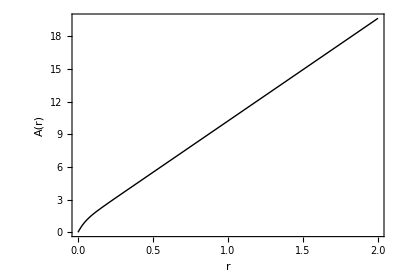

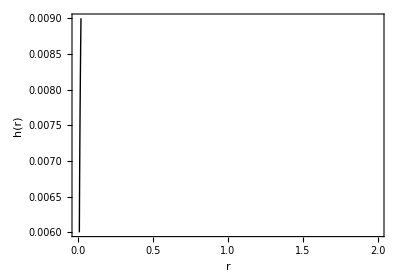

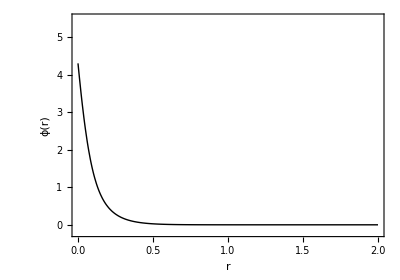

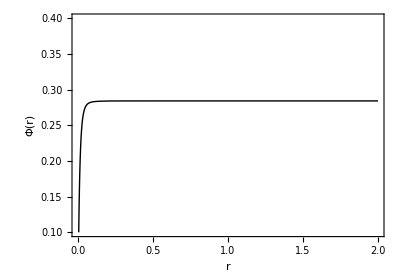

Plot::optx: Unknown option PlotLegends in {Rsol[r], -20}, {r, rstart, rmax}, PlotStyle → {{Black, Thick}, {Blue, Thick, Dashed}}, FrameLabel → {StyleBox[.

Plot[{Rsol[r],-20},{r,rstart,rmax},PlotStyle→{{Black,Thick},{Blue,Thick,Dashed}},FrameLabel→{r,R(r)},LabelStyle→Directive[Black,16],AspectRatio→0.7,Frame→True,PlotRange→{-140.,-12},PlotLegends→Placed[{numerical solution,UV boundary asymptotics},Right]]

{ | Estimate | Standard Error | t-Statistic | P-Value
phiA | 6.48614 | 3.17797×10^-6 | 2.04097×10^6 | 3.67824027686×10^-4812, | DF | SS | MS
Model | 1 | 2.98936×10^-6 | 2.98936×10^-6
Error | 1000 | 7.17638×10^-16 | 7.17638×10^-19
Uncorrected Total | 1001 | 2.98936×10^-6 | 
Corrected Total | 1000 | 2.35568×10^-6 | }

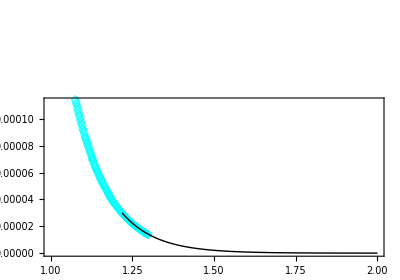

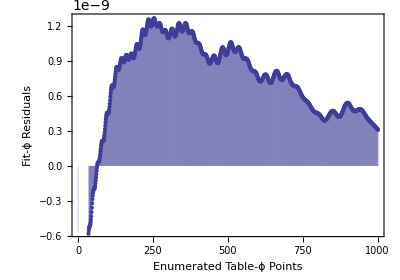

{ | Estimate | Standard Error | t-Statistic | P-Value
A0far | 0.795231 | 3.78332×10^-9 | 2.10194×10^8 | 6.04671548829×10^-6825, | DF | SS | MS
Model | 1 | 230437. | 230437.
Error | 1000 | 1.43278×10^-11 | 1.43278×10^-14
Uncorrected Total | 1001 | 230437. | 
Corrected Total | 1000 | 7418.09 | }

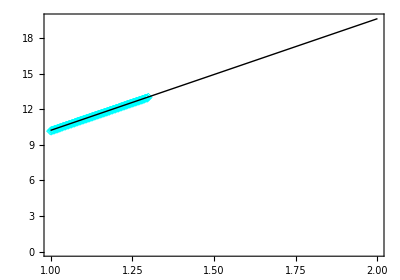

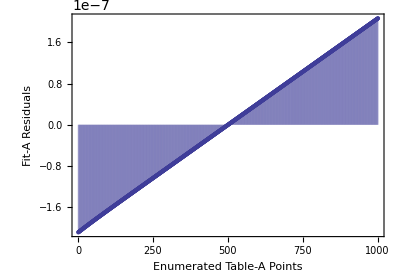

{ϕ_A,h_0^far,Φ_0^far,Φ_2^far,A_0^far}={6.48614,0.0112675,0.284177,-0.0132143,0.795231}

{T[MeV],μ[MeV],s[MeV^3],ρ[MeV^3]}={96.3927,344.225,1.0685×10^6,21170.2}

```mathematica
(* Numerical solutions for the initial conditions (phi0,Phi1) specified below; for any chosen value of phi0, we must have Phi1 < Subscript[Φ, 1]^max(Subscript[ϕ, 0])=√(-(2 V(phi0))/(f(phi0))) and one must also check that A[r] is a monotonically increasing function of r: *)
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=4.3;
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=0.2 boundPhi1;
Print["{ϕ_0,Log(ϕ_0),Φ_1,Φ_1^max(ϕ_0),Φ_1/Φ_1^max}","=",{phi0,N[Log[phi0]],Phi1,boundPhi1,Phi1/boundPhi1}]

sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax} ]
Plot[{Evaluate[A[r]/.sol]},{r,rstart,rmax},PlotStyle->{{Black,Thick}},FrameLabel->{Style["r",20,Bold],Style["A(r)",20,Bold]},LabelStyle->Directive[Black,16],AspectRatio->0.7,Frame->True]
Plot[{Evaluate[h[r]/.sol]},{r,rstart,rmax},PlotStyle->{{Black,Thick}},FrameLabel->{Style["r",20,Bold],Style["h(r)",20,Bold]},LabelStyle->Directive[Black,16],AspectRatio->0.7,Frame->True,PlotRange->{0.006,0.009}]
Plot[{Evaluate[ϕ[r]/.sol]},{r,rstart,rmax},PlotStyle->{{Black,Thick}},FrameLabel->{Style["r",20,Bold],Style["ϕ(r)",20,Bold]},LabelStyle->Directive[Black,16],AspectRatio->0.7,Frame->True,PlotRange->{-0.2,5.5}]
Plot[{Evaluate[Φ[r]/.sol]},{r,rstart,rmax},PlotStyle->{{Black,Thick}},FrameLabel->{Style["r",20,Bold],Style["Φ(r)",20,Bold]},LabelStyle->Directive[Black,16],AspectRatio->0.7,Frame->True,PlotRange->{0.1,0.4}]

(* Ricci scalar of the above solution - for asymptotically AdS_5 geometries, it must satisfy R(r->∞)->-20]: *)
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Plot[{Rsol[r],-20},{r,rstart,rmax},PlotStyle->{{Black,Thick},{Blue,Thick,Dashed}},FrameLabel->{Style["r",20,Bold],Style["R(r)",20,Bold]},LabelStyle->Directive[Black,16],AspectRatio->0.7,Frame->True,PlotRange->{-140.,-12},PlotLegends->Placed[{"numerical solution","UV boundary asymptotics"},Right]]

(* Fits for the far from the horizon (near-boundary) asymptotics: *)
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];

tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
plottableϕ=ListPlot[{tableϕ},Joined->False,Frame->True,FrameLabel->{Style["r",20,Bold],Style["ϕ(r)",20,Bold]},PlotStyle->{{Cyan,Thick}},PlotMarkers->{{"◇"}},LabelStyle->Directive[Black,16],AspectRatio->0.7];
plotfitϕ=Plot[{Evaluate[(phiA Exp[-ν Asol[r]])/.fitϕ]},{r,1,rmax},Frame->True,FrameLabel->{Style["r",20,Bold],Style["ϕ(r)",20,Bold]},PlotStyle->{{Black,Thick}},LabelStyle->Directive[Black,16],AspectRatio->0.7,PlotRange->{-0.2,0.00003}];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA[{"ParameterTable","ANOVATable"}]
Show[plottableϕ,plotfitϕ]
ListPlot[{testphiA["FitResiduals"]},Joined->False,Filling->Axis,Frame->True,FrameLabel->{Style["Enumerated Table-ϕ Points",20,Bold],Style["Fit-ϕ Residuals",20,Bold]},LabelStyle->Directive[Black,16],AspectRatio->0.7]

tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
plottableA=ListPlot[{tableA},Joined->False,Frame->True,FrameLabel->{Style["r",20,Bold],Style["A(r)",20,Bold]},PlotStyle->{{Cyan,Thick}},PlotMarkers->{{"◇"}},LabelStyle->Directive[Black,16],AspectRatio->0.7];
plotfitA=Plot[{Evaluate[(r/(L Sqrt[hsol[rmax]])+A0far)/.fitA]},{r,1,rmax},Frame->True,FrameLabel->{Style["r",20,Bold],Style["A(r)",20,Bold]},PlotStyle->{{Black,Thick}},LabelStyle->Directive[Black,16],AspectRatio->0.7];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far[{"ParameterTable","ANOVATable"}]
Show[plottableA,plotfitA]
ListPlot[{testA0far["FitResiduals"]},Joined->False,Filling->Axis,Frame->True,FrameLabel->{Style["Enumerated Table-A Points",20,Bold],Style["Fit-A Residuals",20,Bold]},LabelStyle->Directive[Black,16],AspectRatio->0.7]

(* Relevant parameters for the calculation of thermodynamical quantities: *)
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4)) (* Phi2far is evaluated via Gauss conserved charge *);
A0far=fitA[[1,2]] (* A0far appears in the counterterms that renormalize Polyakov and Wilson loops *);
Print["{ϕ_A,h_0^far,Φ_0^far,Φ_2^far,A_0^far}","=",{phiA,h0far,Phi0far,Phi2far,A0far}]

(* THERMODYNAMICAL QUANTITIES WITH UNITS: *)
Clear[T,μ,s,ρ];
T=1/(4 Pi L Abs[phiA]^(1/ν) Sqrt[h0far]) lambda;
μ=Phi0far/(L Abs[phiA]^(1/ν) Sqrt[h0far]) lambda;
s=(2 Pi)/(κ2 Abs[phiA]^(3/ν)) lambda^3;
ρ=-Phi2far/(κ2 Abs[phiA]^(3/ν) Sqrt[h0far]) lambda^3;
Print["{T[MeV],μ[MeV],s[MeV^3],ρ[MeV^3]}","=",{T,μ,s,ρ}]
```

## Generate relevant backgrounds

### Generate the backgrounds in a rectangular (ϕ0,ΦRel) grid and export / import

#### The code that loops over the backgrounds (takes a min or so to execute at current grid size)

```mathematica
(*MList={};SList={};
ProgressIndicator[Dynamic[ϕ0Loop],{0.5,4.3}]
Do[
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=ϕ0Loop;
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=ΦRelLoop* boundPhi1;

sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax} ];
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];
tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4));
A0far=fitA[[1,2]];
Clear[T,μ,s,ρ];
T=(1/(4 Pi L Abs[phiA]^(1/ν) Sqrt[h0far])) lambda;
μ=(Phi0far/(L Abs[phiA]^(1/ν) Sqrt[h0far])) lambda;
MList=Append[MList,{μ,ϕ0Loop,ΦRelLoop,T}];
SList=Append[SList,{μ,T}];
,{ϕ0Loop,0.5,4.3,0.05},{ΦRelLoop,0,0.25,0.005}]*)
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["Backgrounds-Corrected.dat",MList];*)
```

#### Import it, the data is in the (μ,ϕ0,ΦRel,T) format, and generate the simpler list containing only the pairs (μ,T)

```mathematica
MList=Import["Backgrounds-Corrected.dat"];
SList=Table[{MList[[i,1]],MList[[i,4]]},{i,1,Length[MList]}];
```

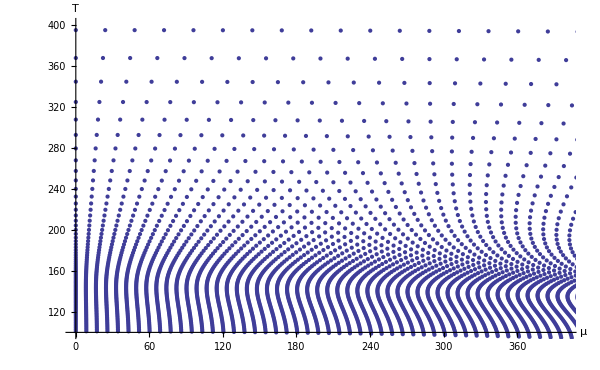

```mathematica
ListPlot[SList,AxesLabel->{"μ","T"},PlotRange->{{0,400},{100,400}},ImageSize->600]
```

### Illustrate the interpolation method

#### What we want is to get ϕ0 and ΦRel for a given pair of (μ,T), which is like multi-valued (vector) interpolation of function of two variables, which I think Mathematica can’t do

#### To illustrate this, let’s look at the (μ,T) plane of generated backgrounds and draw lines of constant ϕ0=1 (blue) and ΦRel=0.1 (red)

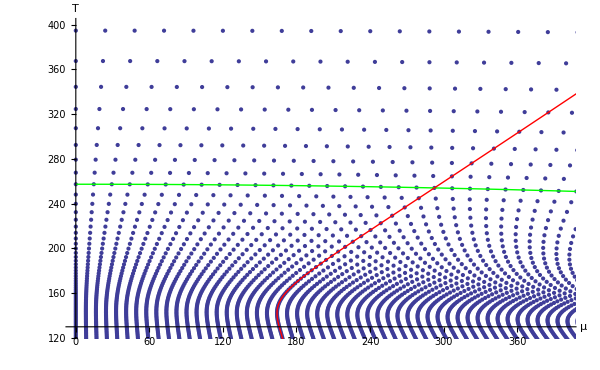

```mathematica
TL={};TP={};
Do[
If[MList[[i,2]]==1,TL=Append[TL,{MList[[i,1]],MList[[i,4]]}]];
If[MList[[i,3]]==0.1,TP=Append[TP,{MList[[i,1]],MList[[i,4]]}]];
,{i,1,Length[MList]}]
Show[
ListPlot[SList,AxesLabel->{"μ","T"},PlotRange->{{0,400},{125,400}},ImageSize->600],
ListPlot[{TL,TP},Joined->True,PlotStyle->{Green,Red}]
]
```

#### The idea is to isolate the four nearest neighbors in the four quadrants (upper right, down right, etc.) for a test point that has μ = 200 and T = 250

```mathematica
μTest=200;Temp=250;
MinUL=1000;MinDL=1000;MinUR=1000;MinDR=1000;
Do[
μLocal=MList[[i,1]];
TLocal=MList[[i,4]];
DistLocal=√((μTest-μLocal)^2+(Temp-TLocal)^2);
If[DistLocal<MinDL&&μLocal≤μTest&&TLocal≤Temp,{MinDL=DistLocal;,LLLoc=i;}];
If[DistLocal<MinUL&&μLocal≤μTest&&TLocal≥Temp,{MinUL=DistLocal;,ULLoc=i;}];
If[DistLocal<MinDR&&μLocal≥μTest&&TLocal≤Temp,{MinDR=DistLocal;,LRLoc=i;}];
If[DistLocal<MinUR&&μLocal≥μTest&&TLocal≥Temp,{MinUR=DistLocal;,URLoc=i;}];
,{i,1,Length[MList]}]
```

#### Let’s see this

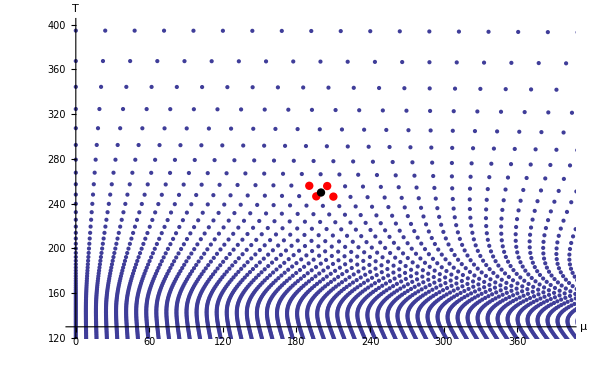

```mathematica
Show[
ListPlot[SList,AxesLabel->{"μ","T"},PlotRange->{{0,400},{125,400}},ImageSize->600],
Graphics[{PointSize->0.01,Red,Point[{SList[[LLLoc,1]],SList[[LLLoc,2]]}]}],
Graphics[{PointSize->0.01,Red,Point[{SList[[ULLoc,1]],SList[[ULLoc,2]]}]}],
Graphics[{PointSize->0.01,Red,Point[{SList[[LRLoc,1]],SList[[LRLoc,2]]}]}],
Graphics[{PointSize->0.01,Red,Point[{SList[[URLoc,1]],SList[[URLoc,2]]}]}],
Graphics[{PointSize->0.01,Black,Point[{μTest,Temp}]}]
]
```

#### Now we know that the (ϕ0,ΦRel) for our point of interest is in between the (ϕ0,ΦRel) of those points. Obviously, the lower left is the closest one, so somehow in taking the weighted average we need to assign the greatest weight to that one.

#### My idea is to do w_1=(d2*d3*d4)/(d2*d3*d4 + d1*d3*d4 + d1*d2*d4 + d1*d2*d3) , and so on, because: a.) It obviously assigns higher weight to point 1 the greater the other distances are b.) For vanishing d2 and/or d3 and/or d4 it becomes zero c.) For vanishing d1, it becomes 1 d.) It is normalized

```mathematica
ExList={MList[[LLLoc]],MList[[ULLoc]],MList[[LRLoc]],MList[[URLoc]]};
Do[Dist[i]=√((μTest-ExList[[i,1]])^2+(Temp-ExList[[i,4]])^2);,{i,1,4}];
Norma=Sum[Product[Dist[j]^(1-KroneckerDelta[i,j]),{j,1,4}],{i,1,4}];
Do[Weight[i]=Product[Dist[j]^(1-KroneckerDelta[i,j]),{j,1,4}]/Norma,{i,1,4}];
```

#### Let’s check that the weights correspond to our expectations from the above image

```mathematica
{{Weight[2],Weight[4]},{Weight[1],Weight[3]}}//TableForm
```

0.175219 | 0.25772
0.382923 | 0.184137

#### Now we can compute the average ϕ0 and ΦRel using these weights

```mathematica
ϕ0Av=Sum[Weight[i]*ExList[[i,2]],{i,1,4}];
ΦRelAv=Sum[Weight[i]*ExList[[i,3]],{i,1,4}];
```

#### Let’s finally see how good we are:

```mathematica
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=ϕ0Av;
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=ΦRelAv* boundPhi1;

sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax} ];
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];
tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4));
A0far=fitA[[1,2]];
Clear[T,μ,s,ρ];
T=(1/(4 Pi L Abs[phiA]^(1/ν) Sqrt[h0far])) lambda
μ=(Phi0far/(L Abs[phiA]^(1/ν) Sqrt[h0far])) lambda
```

250.43

200.002

### Construct the backgrounds one is interested in

#### Make a list of desired backgrounds in the (μ,T) format

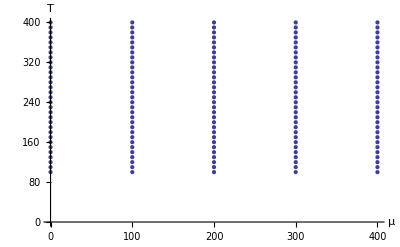

```mathematica
MyBkgList=Flatten[Table[{μi,Ti},{μi,0,400,100},{Ti,100,400,10}],1];
ListPlot[MyBkgList,AxesLabel->{"μ","T"}]
```

#### Generate the backgrounds using the previous procedure

```mathematica
DataIC={};
μCheckList={};TCheckList={};RCheckList={};
Do[
(* Find the ϕ0 and ΦRel that correspond to the background of interest using the previous interpolation method *)
μTest=MyBkgList[[kk,1]];
Temp=MyBkgList[[kk,2]];
MinUL=1000;MinDL=1000;MinUR=1000;MinDR=1000;
Do[
μLocal=MList[[i,1]];
TLocal=MList[[i,4]];
DistLocal=√((μTest-μLocal)^2+(Temp-TLocal)^2);
If[DistLocal<MinDL&&μLocal≤μTest&&TLocal≤Temp,{MinDL=DistLocal;,LLLoc=i;}];
If[DistLocal<MinUL&&μLocal≤μTest&&TLocal≥Temp,{MinUL=DistLocal;,ULLoc=i;}];
If[DistLocal<MinDR&&μLocal≥μTest&&TLocal≤Temp,{MinDR=DistLocal;,LRLoc=i;}];
If[DistLocal<MinUR&&μLocal≥μTest&&TLocal≥Temp,{MinUR=DistLocal;,URLoc=i;}];
,{i,1,Length[MList]}];
ExList={MList[[LLLoc]],MList[[ULLoc]],MList[[LRLoc]],MList[[URLoc]]};
Do[Dist[i]=√((μTest-ExList[[i,1]])^2+(Temp-ExList[[i,4]])^2);,{i,1,4}];
Norma=Sum[Product[Dist[j]^(1-KroneckerDelta[i,j]),{j,1,4}],{i,1,4}];
Do[Weight[i]=Product[Dist[j]^(1-KroneckerDelta[i,j]),{j,1,4}]/Norma,{i,1,4}];
ϕ0Av=Sum[Weight[i]*ExList[[i,2]],{i,1,4}];
ΦRelAv=Sum[Weight[i]*ExList[[i,3]],{i,1,4}];
(* Solve for the background for these initial conditions: *)
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=ϕ0Av;
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=ΦRelAv* boundPhi1;

sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax} ];
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];
tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4));
A0far=fitA[[1,2]];
Clear[T,μ,s,ρ];
T=(1/(4 Pi L Abs[phiA]^(1/ν) Sqrt[h0far])) lambda;
μ=(Phi0far/(L Abs[phiA]^(1/ν) Sqrt[h0far])) lambda;
(* Save the results: *)
DataIC=Append[DataIC,{μ,ϕ0Av,ΦRelAv,T}];
μCheckList=Append[μCheckList,{kk,If[μTest≠0,(μ-μTest)/μTest,0]}];
TCheckList=Append[TCheckList,{kk,(T-Temp)/Temp}];
RCheckList=Append[RCheckList,{kk,(-20-Rsol[0.99rmax])/-20}];
,{kk,1,Length[MyBkgList]}]
```

#### Make sure that the error is reasonably small, and that the generated backgrounds asymptote to AdS5

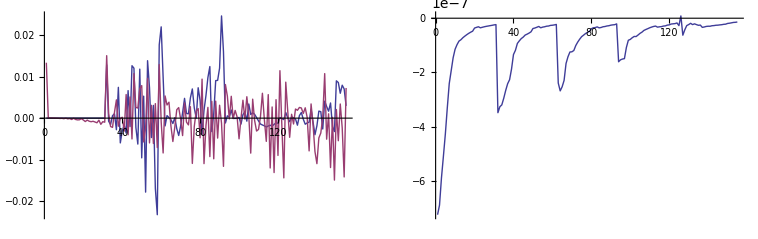

```mathematica
GraphicsGrid[
{{
ListPlot[{μCheckList,TCheckList},PlotRange->All,AxesOrigin->{0,0},Joined->True,ImageSize->350],
ListPlot[RCheckList,PlotRange->All,AxesOrigin->{0,0},Joined->True]
}}]
```

#### The initial conditions are saved in the table DataIC of the same format as before (also check that the actual numbers look reasonable)

```mathematica
DataICDisplay=Join[{{Style["μ",Bold],Style["ϕ_0",Bold],Style["Φ_rel",Bold],Style["T",Bold]}},DataIC];
Grid[DataICDisplay,Dividers->{{False,True,True,True,False,False,False,False,True},{False,True}},Background->{{},{LightGray}}];
```

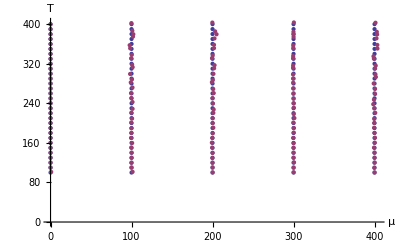

```mathematica
ListPlot[{MyBkgList,Table[{DataIC[[i,1]],DataIC[[i,4]]},{i,1,Length[DataIC]}]},AxesLabel->{"μ","T"}(*,PlotLegends->{"Wanted values","Actual values"}*)]
```

## EF metric and KG equation

### Set up the metric

```mathematica
SetDirectory[NotebookDirectory[]];
<<GRtensors
```

#### Metric in the EF coordinates (note that the off diagonal elements are positive here, as opposed to in Janik’s paper)

```mathematica
ggValues={
{-h[r]*Exp[2A[r]],0,0,0,ⅇ^(A[r]+B[r])},
{0,Exp[2A[r]],0,0,0},
{0,0,Exp[2A[r]],0,0},
{0,0,0,Exp[2A[r]],0},
{ⅇ^(A[r]+B[r]),0,0,0,0}
};
ggiValues=Inverse[ggValues];
SetXMet[{t,x1,x2,x3,r},ggValues,ggiValues];
NewTensor[chris,chrisDef,Simplify]
DisplayTensor[gg]//MatrixForm
detg=Det[DisplayTensor[gg]];
```

gg[{DownVector,DownVector}] has components

(-ⅇ^(2 A[r]) h[r] | 0 | 0 | 0 | ⅇ^A[r]
0 | ⅇ^(2 A[r]) | 0 | 0 | 0
0 | 0 | ⅇ^(2 A[r]) | 0 | 0
0 | 0 | 0 | ⅇ^(2 A[r]) | 0
ⅇ^A[r] | 0 | 0 | 0 | 0)

gg[{DownVector,DownVector}] has components

```mathematica
XμValues={t,x1,x2,x3,r};
XμDef[DefaultIndexType]={UpVector};
XμDef[{m_}]:=XμValues[[m]];
NewTensor[Xμ,XμDef]
```

#### ANum and hNum will be the numerical solutions

```mathematica
NumRules={A->Function[r,ANum[r]],h->Function[r,hNum[r]]};
```

### Klein-Gordon equation

#### Look for harmonic solutions

```mathematica
ϕRule={ϕ->Function[{t,x1,x2,x3,r},Exp[-ⅈ*ω*t+ⅈ*k1*x1+ⅈ*k2*x2+ⅈ*k3*x3]*ψ[r]]};
```

#### D’Alembertian operator

```mathematica
Boxϕ=1/(√-detg)Sum[D[√-detg*Sum[gg[{{μ,UpVector},{ν,UpVector}}]*D[ϕ[t,x1,x2,x3,r]/.ϕRule,Xμ[{μ}]],{μ,1,dim}],Xμ[{ν}]],{ν,1,dim}];
```

#### Plug in the harmonic solution and clean it up

```mathematica
OnShellBox=Boxϕ*Exp[+ⅈ*ω*t-ⅈ*k1*x1-ⅈ*k2*x2-ⅈ*k3*x3] ⅇ^(2 (A[r]+B[r]))/.k1^2->k^2-k2^2-k3^2//Simplify
```

-ψ[r] (k^2+3 ⅈ ⅇ^A[r] ω A'[r])+ⅇ^A[r] ((-2 ⅈ ω+4 ⅇ^A[r] h[r] A'[r]+ⅇ^A[r] h'[r]) ψ'[r]+ⅇ^A[r] h[r] ψ''[r])

## Compute QNM for one background using shooting method

### Choose and solve for the background

#### Choose some particular background

```mathematica
iTemp=15;
DataIC[[iTemp]]
```

{0.,1.0993,0.,239.994}

#### Solve for the metric

```mathematica
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=DataIC[[iTemp,2]];
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=DataIC[[iTemp,3]]* boundPhi1;

sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax},AccuracyGoal->60];
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];
tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4));
A0far=fitA[[1,2]];
```

### Set up the QNM equation

#### I like 0802.0775 for some nice explanations

#### We want to solve the following equation for ψ

```mathematica
KGSimp=ⅇ^(-A[r])OnShellBox//Simplify
```

ψ[r] (-ⅇ^(-A[r]) k^2-3 ⅈ ω A'[r])+(-2 ⅈ ω+4 ⅇ^A[r] h[r] A'[r]+ⅇ^A[r] h'[r]) ψ'[r]+ⅇ^A[r] h[r] ψ''[r]

#### We impose regularity at the horizon and demand that we get ψ -> 0 at infinity. The idea is to choose some complex ω and solve this equation for ψ and see if we got it to be zero at infinity. If not, we try another ω.

#### We start integration from the horizon so we have to know value of ψ and its derivative close to the horizon. We’ll need the series expansion for h(r) and A(r)

```mathematica
hSerRul={h->Function[r,0+1*r+Ch2*r^2]};
ASerRul={A->Function[r,0+CA1*r+CA2*r^2]};
ψSerRul={ψ->Function[r,ψ0+ψ1*r+ψ2*r^2]};
```

#### Note that the series solution for ψ is just the regular Taylor expansion, i.e. the Frobenius coefficient is zero, since we’re in the ingoing EF coordinates

```mathematica
ψ1Rule=Solve[(Series[KGSimp/.hSerRul/.ASerRul/.ψSerRul,{r,0,0}]//Normal)==0,ψ1][[1]]//Simplify
```

{ψ1→(ⅈ ψ0 (k^2+3 ⅈ CA1 ω))/(ⅈ+2 ω)}

#### We know what A1 is supposed to be (2.16 in manuscript)

```mathematica
CA1Rule={CA1->A1};
```

#### Just to make sure we have the right numbers

```mathematica
{A1,-1/6*(2Vphi0+fphi0*Phi1^2)}
```

{4.68439,4.68439}

#### We will look for complex ω:

```mathematica
ωRule={ω->Reω+ⅈ*Imω};
```

#### Hence we have

```mathematica
ψ1Num=ψ1/.ψ1Rule/.ψ0->1/.CA1Rule/.ωRule
```

(ⅈ (k^2+(0.+14.0532 ⅈ) (ⅈ Imω+Reω)))/(ⅈ+2 (ⅈ Imω+Reω))

### Run the code and find ω (for k = 0)

#### The idea is to solve the KG equation on some grid of complex ω, and find the value of |ψ| close to the boundary

#### Select the number of steps

```mathematica
ImωMin=-2;ImωMax=-0.1;ImωStep=0.03;
ReωMin=0.1;ReωMax=2;ReωStep=0.03;
```

#### The code

```mathematica
ProgressIndicator[Dynamic[ReωLocal],{ReωMin,ReωMax}]
Res={};Ims={};Counter=0;
Do[
llSol=NDSolve[{
(KGSimp/.A->Function[r,Asol[r]]/.h->Function[r,hsol[r]]/.ωRule/.Reω->ReωLocal/.Imω->ImωLocal/.ψ->ll/.k->0)==0,
ll[rstart]==1,ll'[rstart]==(ψ1Num/.Reω->ReωLocal/.Imω->ImωLocal/.k->0)},
ll,{r,rstart,rmax}][[1]];
Res=Append[Res,{ReωLocal,ImωLocal,Re[ll[0.98rmax]/.llSol]}];
Ims=Append[Ims,{ReωLocal,ImωLocal,Im[ll[0.98rmax]/.llSol]}];
,{ReωLocal,ReωMin,ReωMax,ReωStep},{ImωLocal,ImωMin,ImωMax,ImωStep}]
```

#### Find the absolute values of ψ and their minimum

```mathematica
Abss=Table[{Res[[i,1]],Res[[i,2]],√(Res[[i,3]]^2+Ims[[i,3]]^2)},{i,1,Length[Res]}];
MinVal=Min[Table[{Abss[[i,3]]},{i,1,Length[Abss]}]];
```

#### Now let’s look at all the points in the complex ω plane whose |ψ| < 8 MinVal, and color them according to their values

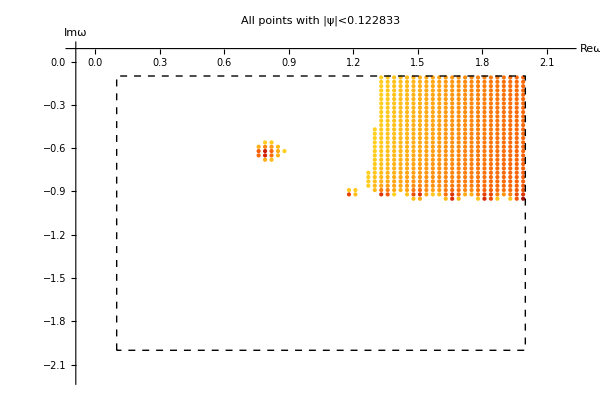
-Graphics- | RGBColor[1.,0.820127,0.126955] | 0.122833
RGBColor[1.,0.750848,0.108241] | 0.11055
RGBColor[1.,0.681569,0.0895277] | 0.0982668
RGBColor[0.993993,0.592759,0.0705943] | 0.0859834
RGBColor[0.981978,0.48442,0.0514412] | 0.0737001
RGBColor[0.969963,0.376081,0.0322881] | 0.0614167
RGBColor[0.910829,0.274539,0.0209552] | 0.0491334
RGBColor[0.851696,0.172996,0.00962234] | 0.03685
RGBColor[0.751452,0.09778,0.00632944] | 0.0245667
RGBColor[0.610097,0.04889,0.0110765] | 0.0122833

```mathematica
Lim=8MinVal;
AbsFine={};AbsValFine={};
Do[
If[Abss[[i,3]]<Lim,{
AbsFine=Append[AbsFine,{Abss[[i,1]],Abss[[i,2]]}],
AbsValFine=Append[AbsValFine,{Abss[[i,3]]}]}];
,{i,1,Length[Abss]}]
ScatPlot=Show[Graphics[
Table[{PointSize[Medium],ColorData["SolarColors"]@(AbsValFine[[i,1]]/Lim),Point[AbsFine[[i]]]},{i,1,Length[AbsFine]}],Axes->True,PlotRange->{{ReωMin-0.1(ReωMax-ReωMin),ReωMax+0.1(ReωMax-ReωMin)},{ImωMin-0.1(ImωMax-ImωMin),ImωMax+0.1(ImωMax-ImωMin)}},AxesOrigin->{ReωMin-0.1(ReωMax-ReωMin),ImωMax+0.1(ImωMax-ImωMin)},AspectRatio->0.7,ImageSize->600,AxesLabel->{"Reω","Imω"},PlotLabel->"All points with |ψ|<"<>ToString[Lim]],
Graphics[{Black,Dashed,Line[{{ReωMin,ImωMin},{ReωMin,ImωMax},{ReωMax,ImωMax},{ReωMax,ImωMin},{ReωMin,ImωMin}}]}]];
Grid[{{ScatPlot,
Grid[Table[{ColorData["SolarColors"]@i,i*Lim},{i,1,0.1,-0.1}],Spacings->{0,0},Alignment->Left]}}]
```

#### We can clearly see a cluster, and what we will do in the following sections is to put this inside a Manipulate, and then change the value of this coefficient α in |ψ| < α MinVal, until we can clearly see a cluster and then continue to narrow it down, until we get only one point in that cluster, and this will be our rough estimate for ω_0

#### In later sections, we will use these rough values as seed for a finer grid in ω, centered around these rough values

## Code for k = 0, rough grid

### Prepare the code

#### Select range of backrounds one is interested in

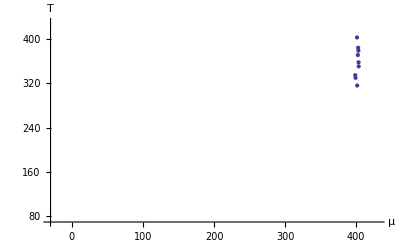

```mathematica
BkgOfInterest=Table[iTemp,{iTemp,147,Length[DataIC],1}];
ListPlot[Table[{DataIC[[BkgOfInterest[[iTemp]],1]],DataIC[[BkgOfInterest[[iTemp]],4]]},{iTemp,1,Length[BkgOfInterest],1}],PlotRange->{{-30,430},{70,430}},AxesLabel->{"μ","T"},AxesOrigin->{-30,70}]
```

#### Set up the grid

```mathematica
ImωMin=-2;ImωMax=-0.1;ImωStep=0.03;
ReωMin=0.1;ReωMax=2;ReωStep=0.03;
NSteps=Length[Flatten[Table[1,{ReωLocal,ReωMin,ReωMax,ReωStep},{ImωLocal,ImωMin,ImωMax,ImωStep}]]]
```

4096

### Solve QNM for all the backgrounds

#### This code will now run over these backgrounds, and for each background, save a list of |ψ| in a separate data file in the “Data” folder, that we can then use later for analysis and plotting

```mathematica
Counter=1;
ProgressIndicator[Dynamic[ReωLocal],{ReωMin,ReωMax}]
Grid[{{"Background: ",Dynamic[Counter]," / ",Length[BkgOfInterest]}}]
Clear[Abss];
Do[
(* ------------------------------------------------------------------------------------ *)
(* ---------- Solve for the bacgkround ------------------------------------------------ *)
(* ------------------------------------------------------------------------------------ *)
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=DataIC[[iTemp,2]];
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=DataIC[[iTemp,3]]* boundPhi1;
sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax},AccuracyGoal->60];
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];
tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4));
A0far=fitA[[1,2]];
(* -------------------------------------------------------------------------------------------- *)
(* ---------- Step up the QNM equation -------------------------------------------------------- *)
(* -------------------------------------------------------------------------------------------- *)
KGSimp=ⅇ^(-A[r])OnShellBox/.k->0//Simplify;
hSerRul={h->Function[r,0+1*r+Ch2*r^2]};
ASerRul={A->Function[r,0+CA1*r+CA2*r^2]};
ψSerRul={ψ->Function[r,ψ0+ψ1*r+ψ2*r^2]};
ψ1Rule=Solve[(Series[KGSimp/.hSerRul/.ASerRul/.ψSerRul,{r,0,0}]//Normal)==0,ψ1][[1]];
CA1Rule={CA1->A1};
ωRule={ω->Reω+ⅈ*Imω};
ψ1Num=ψ1/.ψ1Rule/.ψ0->1/.CA1Rule/.ωRule;
(* --------------------------------------------------------------------------------------------- *)
(* ---------- The code ------------------------------------------------------------------------- *)
(* --------------------------------------------------------------------------------------------- *)
Res={};Ims={};
Do[
llSol=NDSolve[{
(KGSimp/.A->Function[r,Asol[r]]/.h->Function[r,hsol[r]]/.ωRule/.Reω->ReωLocal/.Imω->ImωLocal/.ψ->ll)==0,
ll[rstart]==1,ll'[rstart]==(ψ1Num/.Reω->ReωLocal/.Imω->ImωLocal)},
ll,{r,rstart,rmax}][[1]];
Res=Append[Res,{ReωLocal,ImωLocal,Re[ll[0.98rmax]/.llSol]}];
Ims=Append[Ims,{ReωLocal,ImωLocal,Im[ll[0.98rmax]/.llSol]}];
,{ReωLocal,ReωMin,ReωMax,ReωStep},{ImωLocal,ImωMin,ImωMax,ImωStep}];
(* ----------------------------------------------------------------------------------------------- *)
(* ---------- Save the results ------------------------------------------------------------------- *)
(* ----------------------------------------------------------------------------------------------- *)
Abss=Table[√(Res[[i,3]]^2+Ims[[i,3]]^2),{i,1,Length[Res]}];
Export["Data/Abs"<>ToString[iTemp]<>".dat",Abss];
Counter=Counter+1;
,{iTemp,BkgOfInterest}]
```

### Find max value of ψ for clear clusters

#### Now, for every background, as explained before, we play with the slider until we visually indentify a cluster in the complex ω plane, and then continue to reduce the max value of |ψ| until there is only one point left in it

```mathematica
iTemp=155;
Abss=Flatten[Import["Data/Abs"<>ToString[iTemp]<>".dat"]];
MinVal=Min[Abss];
ωList=Flatten[Table[{ReωLocal,ImωLocal},{ReωLocal,ReωMin,ReωMax,ReωStep},{ImωLocal,ImωMin,ImωMax,ImωStep}],1];
Manipulate[
Lim=LimCoeff*MinVal;
AbsFine={};AbsValFine={};
Do[
If[Abss[[i]]<Lim,{
AbsFine=Append[AbsFine,{ωList[[i,1]],ωList[[i,2]]}];
AbsValFine=Append[AbsValFine,{Abss[[i]]}];
}];
,{i,1,Length[Abss]}];
ScatPlot=Show[Graphics[
Table[{PointSize[Medium],ColorData["SolarColors"]@(AbsValFine[[i,1]]/Lim),Point[AbsFine[[i]]]},{i,1,Length[AbsFine]}],Axes->True,PlotRange->{{ReωMin-0.1(ReωMax-ReωMin),ReωMax+0.1(ReωMax-ReωMin)},{ImωMin-0.1(ImωMax-ImωMin),ImωMax+0.1(ImωMax-ImωMin)}},AxesOrigin->{ReωMin-0.1(ReωMax-ReωMin),ImωMax+0.1(ImωMax-ImωMin)},AspectRatio->0.7,ImageSize->600,AxesLabel->{"Reω","Imω"},PlotLabel->"All points with |ψ|<"<>ToString[Lim]],
Graphics[{Black,Dashed,Line[{{ReωMin,ImωMin},{ReωMin,ImωMax},{ReωMax,ImωMax},{ReωMax,ImωMin},{ReωMin,ImωMin}}]}]];
Grid[{{
ScatPlot,
Grid[Table[{ColorData["SolarColors"]@i,i*Lim},{i,1,0.1,-0.1}],Spacings->{0,0},Alignment->Left],
ListPlot[Table[{ii,LimList[ii]},{ii,1,Length[DataIC]}],PlotRange->{{0,Length[DataIC]},{0,20}},AxesOrigin->{0,0}]}}]
,{{LimCoeff,15},1.1,20},Button["Save the limit",LimList[iTemp]=LimCoeff;]]
```

#### After all these limits have been saved, put them in a table and export -- this will be fed to the more precise code in the next section

```mathematica
Lims=Table[{ii,LimList[ii]},{ii,125,155}]
```

{{125,4.94},{126,2.56},{127,4.18},{128,2.62},{129,4.86},{130,3.96},{131,4.3},{132,1.1},{133,2.02},{134,1.42},{135,1.84},{136,2.6},{137,2.94},{138,2.36},{139,1.6},{140,1.36},{141,1.54},{142,1.84},{143,3.38},{144,4.96},{145,5.7},{146,5.72},{147,6.66},{148,6.92},{149,7.18},{150,5.36},{151,6.1},{152,4.94},{153,5.36},{154,4.96},{155,4.42}}

```mathematica
(*Export["Data/Lims-Set5.dat",Lims];*)
```

## Code for k = 0, fine grid

### Prepare the code

#### Select range of backrounds one is interested in

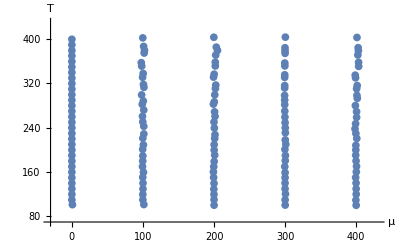

```mathematica
BkgOfInterest=Table[iTemp,{iTemp,1,155,1}];
ListPlot[Table[{DataIC[[BkgOfInterest[[iTemp]],1]],DataIC[[BkgOfInterest[[iTemp]],4]]},{iTemp,1,Length[BkgOfInterest],1}],PlotRange->{{-30,430},{70,430}},AxesLabel->{"μ","T"},AxesOrigin->{-30,70}]
```

#### Load the limits from the visual analysis of the rough code

```mathematica
Lims=Join[
Import["Data/Lims-Set1.dat"],
Import["Data/Lims-Set2.dat"],
Import["Data/Lims-Set3.dat"],
Import["Data/Lims-Set4.dat"],
Import["Data/Lims-Set5.dat"]];
```

#### The rough analysis was made on the following grid

```mathematica
ωRoughList=Flatten[Table[{ReωLocal,ImωLocal},{ReωLocal,0.1,2,0.03},{ImωLocal,-2,-0.1,0.03}],1];
```

### Solve QNM for all the backgrounds

#### Sub-select which of the backrounds we want to compute

```mathematica
iTempStart=63;
iTempStop=155;
```

#### The idea now is to load the |ψ| data for a particular backgorund that was calculated in the previous section, find the rough value of ω_0, and then make a fine 0.002-step grid around this value, for a box of size of the precision of the previous rough grid (0.03). Then solve the KG equation on this grid, and find the absolute minimum of |ψ|

#### Run the code

```mathematica
Counter=1;
ProgressIndicator[Dynamic[CounterLocal],{1,961}]
Grid[{{"Background: ",Dynamic[Counter]," / ",iTempStop-iTempStart+1}}]
Clear[Abss];
Do[
(* ----------------------------------------------------------------------------------- *)
(* ---------- Define the limits ------------------------------------------------------ *)
(* ----------------------------------------------------------------------------------- *)
AbssRough=Flatten[Import["Data/Abs"<>ToString[iTemp]<>".dat"]];
MinVal=Min[AbssRough];
Lim=Lims[[iTemp,2]]*MinVal;
AbsFine={};
Do[If[AbssRough[[i]]<Lim,{AbsFine=Append[AbsFine,{ωRoughList[[i,1]],ωRoughList[[i,2]]}];}];,{i,1,Length[AbssRough]}];
ReωArrayStart=Sort[AbsFine][[1,1]];
ImωArrayStart=Sort[AbsFine][[1,2]];
ImωMin=ImωArrayStart-0.03;ImωMax=ImωArrayStart+0.03;ImωStep=0.002;
ReωMin=ReωArrayStart-0.03;ReωMax=ReωArrayStart+0.03;ReωStep=0.002;
ωList=Flatten[Table[{ReωLocal,ImωLocal},{ReωLocal,ReωMin,ReωMax,ReωStep},{ImωLocal,ImωMin,ImωMax,ImωStep}],1];
(* ------------------------------------------------------------------------------------- *)
(* ---------- Solve for the bacgkround ------------------------------------------------- *)
(* ------------------------------------------------------------------------------------- *)
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=DataIC[[iTemp,2]];
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=DataIC[[iTemp,3]]* boundPhi1;

sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax},AccuracyGoal->60];
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];
tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4));
A0far=fitA[[1,2]];
(* ------------------------------------------------------------------------------------- *)
(* ---------- Step up the QNM equation ------------------------------------------------- *)
(* ------------------------------------------------------------------------------------- *)
KGSimp=ⅇ^(-A[r])OnShellBox/.k->0//Simplify;
hSerRul={h->Function[r,0+1*r+Ch2*r^2]};
ASerRul={A->Function[r,0+CA1*r+CA2*r^2]};
ψSerRul={ψ->Function[r,ψ0+ψ1*r+ψ2*r^2]};
ψ1Rule=Solve[(Series[KGSimp/.hSerRul/.ASerRul/.ψSerRul,{r,0,0}]//Normal)==0,ψ1][[1]];
CA1Rule={CA1->A1};
ωRule={ω->Reω+ⅈ*Imω};
ψ1Num=ψ1/.ψ1Rule/.ψ0->1/.CA1Rule/.ωRule;
(* ------------------------------------------------------------------------------------- *)
(* ---------- The code ----------------------------------------------------------------- *)
(* ------------------------------------------------------------------------------------- *)
Res={};Ims={};CounterLocal=0;
Do[
llSol=NDSolve[{
(KGSimp/.A->Function[r,Asol[r]]/.h->Function[r,hsol[r]]/.ωRule/.Reω->ReωLocal/.Imω->ImωLocal/.ψ->ll)==0,
ll[rstart]==1,ll'[rstart]==(ψ1Num/.Reω->ReωLocal/.Imω->ImωLocal)},
ll,{r,rstart,rmax}][[1]];
Res=Append[Res,{ReωLocal,ImωLocal,Re[ll[0.98rmax]/.llSol]}];
Ims=Append[Ims,{ReωLocal,ImωLocal,Im[ll[0.98rmax]/.llSol]}];
CounterLocal=CounterLocal+1;
,{ReωLocal,ReωMin,ReωMax,ReωStep},{ImωLocal,ImωMin,ImωMax,ImωStep}];
(* -------------------------------------------------------------------------------------- *)
(* ---------- Save the results ---------------------------------------------------------- *)
(* -------------------------------------------------------------------------------------- *)
Abss=Table[√(Res[[i,3]]^2+Ims[[i,3]]^2),{i,1,Length[Res]}];
ReωArray[iTemp]=ωList[[Ordering[Abss,1][[1]]]][[1]];
ImωArray[iTemp]=ωList[[Ordering[Abss,1][[1]]]][[2]];
Counter=Counter+1;
,{iTemp,iTempStart,iTempStop,1}]
```

#### Save the data

```mathematica
ForExport3=Table[{iTemp,DataIC[[iTemp,1]],DataIC[[iTemp,4]],ReωArray[iTemp],ImωArray[iTemp]},{iTemp,63,93}];
ForExport4=Table[{iTemp,DataIC[[iTemp,1]],DataIC[[iTemp,4]],ReωArray[iTemp],ImωArray[iTemp]},{iTemp,94,124}];
ForExport5=Table[{iTemp,DataIC[[iTemp,1]],DataIC[[iTemp,4]],ReωArray[iTemp],ImωArray[iTemp]},{iTemp,125,155}];
(*Export["Data/QNMFinalSet3-No-Mu-Temp-ReOmega-ImOmega.dat",ForExport3];
Export["Data/QNMFinalSet4-No-Mu-Temp-ReOmega-ImOmega.dat",ForExport4];
Export["Data/QNMFinalSet5-No-Mu-Temp-ReOmega-ImOmega.dat",ForExport5];*)
```

### Plot Imω and Reω

#### Import the values for Reω and Imω

```mathematica
QNMMaster=Join[
Import["Data/QNMFinalSet1-No-Mu-Temp-ReOmega-ImOmega.dat"],
Import["Data/QNMFinalSet2-No-Mu-Temp-ReOmega-ImOmega.dat"],
Import["Data/QNMFinalSet3-No-Mu-Temp-ReOmega-ImOmega.dat"],
Import["Data/QNMFinalSet4-No-Mu-Temp-ReOmega-ImOmega.dat"],
Import["Data/QNMFinalSet5-No-Mu-Temp-ReOmega-ImOmega.dat"]];
```

#### These ω’s are in the numerical gauge, we need to transform back to the physical one: we need ϕA and h0far for all those backgrounds

```mathematica
ConvFactors={};
Do[
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=DataIC[[iTemp,2]];
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=DataIC[[iTemp,3]]* boundPhi1;

sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax},AccuracyGoal->60];
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];
tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4));
A0far=fitA[[1,2]];
ConvFactors=Append[ConvFactors,{phiA^(1/ν)*√h0far}];
,{iTemp,1,155}]
ConvFactors=Flatten[ConvFactors];
```

#### Now save the omega / T in separate lists according to mu

```mathematica
ReωOverTvsTSet1=Table[{QNMMaster[[i,3]],QNMMaster[[i,4]]/ConvFactors[[i]]*lambda/(2*π*QNMMaster[[i,3]])},{i,1,31}];
ImωOverTvsTSet1=Table[{QNMMaster[[i,3]],QNMMaster[[i,5]]/ConvFactors[[i]]*lambda/(2*π*QNMMaster[[i,3]])},{i,1,31}];
```

```mathematica
ReωOverTvsTSet2=Table[{QNMMaster[[i,3]],QNMMaster[[i,4]]/ConvFactors[[i]]*lambda/(2*π*QNMMaster[[i,3]])},{i,32,62}];
ImωOverTvsTSet2=Table[{QNMMaster[[i,3]],QNMMaster[[i,5]]/ConvFactors[[i]]*lambda/(2*π*QNMMaster[[i,3]])},{i,32,62}];
```

```mathematica
ReωOverTvsTSet3=Table[{QNMMaster[[i,3]],QNMMaster[[i,4]]/ConvFactors[[i]]*lambda/(2*π*QNMMaster[[i,3]])},{i,63,93}];
ImωOverTvsTSet3=Table[{QNMMaster[[i,3]],QNMMaster[[i,5]]/ConvFactors[[i]]*lambda/(2*π*QNMMaster[[i,3]])},{i,63,93}];
```

```mathematica
ReωOverTvsTSet4=Table[{QNMMaster[[i,3]],QNMMaster[[i,4]]/ConvFactors[[i]]*lambda/(2*π*QNMMaster[[i,3]])},{i,94,124}];
ImωOverTvsTSet4=Table[{QNMMaster[[i,3]],QNMMaster[[i,5]]/ConvFactors[[i]]*lambda/(2*π*QNMMaster[[i,3]])},{i,94,124}];
```

```mathematica
ReωOverTvsTSet5=Table[{QNMMaster[[i,3]],QNMMaster[[i,4]]/ConvFactors[[i]]*lambda/(2*π*QNMMaster[[i,3]])},{i,125,155}];
ImωOverTvsTSet5=Table[{QNMMaster[[i,3]],QNMMaster[[i,5]]/ConvFactors[[i]]*lambda/(2*π*QNMMaster[[i,3]])},{i,125,155}];
```

#### Interpolate to smoothen them out

```mathematica
Imω1Int=Interpolation[ImωOverTvsTSet1];
Imω2Int=Interpolation[ImωOverTvsTSet2];
Imω3Int=Interpolation[ImωOverTvsTSet3];
Imω4Int=Interpolation[ImωOverTvsTSet4];
Imω5Int=Interpolation[ImωOverTvsTSet5];
```

```mathematica
Reω1Int=Interpolation[ReωOverTvsTSet1];
Reω2Int=Interpolation[ReωOverTvsTSet2];
Reω3Int=Interpolation[ReωOverTvsTSet3];
Reω4Int=Interpolation[ReωOverTvsTSet4];
Reω5Int=Interpolation[ReωOverTvsTSet5];
```

#### Plot

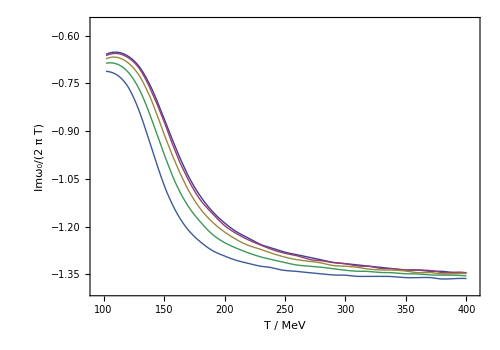

```mathematica
ImsPlot=Plot[{Imω1Int[T],Imω2Int[T],Imω3Int[T],Imω4Int[T],Imω5Int[T]},{T,102,400},
AspectRatio->0.7,AxesOrigin->{0,0},PlotRange->{{95,405},{-1.4,-0.56}},
PlotStyle->Thick,ImageSize->500,Frame->True,Axes->False,LabelStyle->Directive[Black,12],RotateLabel->False,FrameLabel->{Style["T / MeV",FontSize->14,Italic,Bold],Style["Imω_0/(2  π T)",FontSize->14,Italic,Bold]}
(*,PlotLegends->Placed[{"μ = 0 MeV","μ = 100 MeV","μ = 200 MeV","μ = 300 MeV","μ = 400 MeV"},{Scaled[{0.7,0.57}], {0, 0}}]*)]
```

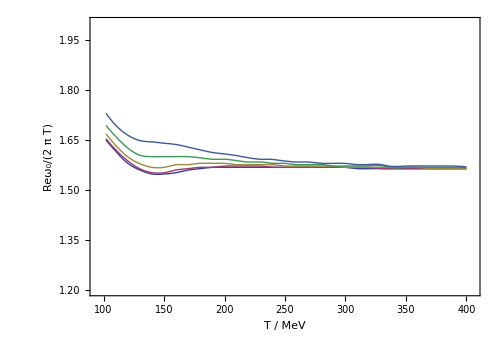

```mathematica
ResPlot=Plot[{Reω1Int[T],Reω2Int[T],Reω3Int[T],Reω4Int[T],Reω5Int[T]},{T,102,400},
AspectRatio->0.7,AxesOrigin->{0,0},PlotRange->{{95,405},{1.2,2}},
PlotStyle->Thick,ImageSize->500,Frame->True,Axes->False,LabelStyle->Directive[Black,12],RotateLabel->False,FrameLabel->{Style["T / MeV",FontSize->14,Italic,Bold],Style["Reω_0/(2  π T)",FontSize->14,Italic,Bold]}
(*,PlotLegends->Placed[{"μ = 0 MeV","μ = 100 MeV","μ = 200 MeV","μ = 300 MeV","μ = 400 MeV"},{Scaled[{0.7,0.57}], {0, 0}}]*)]
```

```mathematica
(*Export["ReOmega.pdf",ResPlot];
Export["ImOmega.pdf",ImsPlot];*)
```

## Fit to Janik’s formula

### Construct the LHS of Janik’s formula

#### CFT value is

```mathematica
ωCFT=-1.373;
```

#### LHS of the formula

```mathematica
LHS[1]=Table[{ImωOverTvsTSet1[[i,1]],ImωOverTvsTSet1[[i,2]]-ωCFT},{i,1,Length[ImωOverTvsTSet1]}];
LHS[2]=Table[{ImωOverTvsTSet2[[i,1]],ImωOverTvsTSet2[[i,2]]-ωCFT},{i,1,Length[ImωOverTvsTSet2]}];
LHS[3]=Table[{ImωOverTvsTSet3[[i,1]],ImωOverTvsTSet3[[i,2]]-ωCFT},{i,1,Length[ImωOverTvsTSet3]}];
LHS[4]=Table[{ImωOverTvsTSet4[[i,1]],ImωOverTvsTSet4[[i,2]]-ωCFT},{i,1,Length[ImωOverTvsTSet4]}];
LHS[5]=Table[{ImωOverTvsTSet5[[i,1]],ImωOverTvsTSet5[[i,2]]-ωCFT},{i,1,Length[ImωOverTvsTSet5]}];
```

#### Interpolate

```mathematica
Do[LHSInt[i]=Interpolation[LHS[i]],{i,1,5}];
```

#### See how it looks like

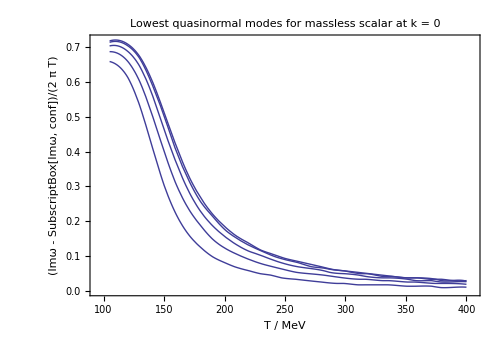

```mathematica
Plot[Table[LHSInt[i][T],{i,1,5}],{T,105,400},
AspectRatio->0.7,AxesOrigin->{0,0},PlotRange->{{95,405},Automatic},
PlotStyle->Thick,ImageSize->500,Frame->True,Axes->False,LabelStyle->Directive[Black,12],RotateLabel->False,FrameLabel->{Style["T / MeV",FontSize->14,Italic,Bold],Style["(Imω - SubscriptBox[Imω, conf])/(2  π T)",FontSize->14,Italic,Bold]},PlotLabel->"Lowest quasinormal modes for massless scalar at k = 0"]
```

### Load the speed of sound data

#### Load the data

```mathematica
SetDirectory[NotebookDirectory[]];
cs2Raw[1]=Import["cs2normaltab0MeV.dat"];
cs2Raw[2]=Import["cs2100MeVtab.dat"];
cs2Raw[3]=Import["cs2200MeVtab.dat"];
cs2Raw[4]=Import["cs2300MeVtab.dat"];
cs2Raw[5]=Import["cs2400MeVtab.dat"];
```

#### Interpolate

```mathematica
Do[cs2Int[i]=Interpolation[cs2Raw[i]],{i,1,5}];
```

#### Plot

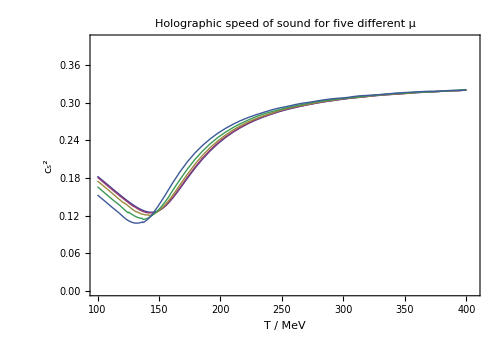

```mathematica
Show[Table[Plot[cs2Int[i][T],{T,100,400},PlotStyle->{Thick,ColorData[1,i]}],{i,1,5}],
FrameLabel->{Style["T / MeV",FontSize->14,Italic,Bold],Style["c_s^2",FontSize->14,Italic,Bold]},
ImageSize->500,Frame->True,Axes->False,LabelStyle->Directive[Black,12],RotateLabel->False,
AspectRatio->0.7,PlotRange->{{100,405},{0,0.4}},
PlotLabel->"Holographic speed of sound for five different μ"]
```

### Pseudospectral code for numerical derivatives

#### Following Boyd’s book: Appendix (F.8) (page 570) for Chebyshev collocation points, and Eq. (5.16) for transformations

#### Set up the grid points and scale to temperature between 100 and 400 (as x goes between -1 and 1)

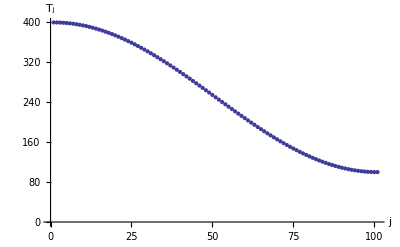

```mathematica
NumPoints=100;
xj=Table[Cos[(π*(i-1))/NumPoints],{i,1,NumPoints+1}]//N;
Tj=250+150*xj;
ListPlot[Tj,AxesLabel->{"j","T_j"}]
```

#### Create the auxiliary array we’ll need later

```mathematica
pj=Table[If[(j==1)||(j==NumPoints+1),2,1],{j,1,NumPoints+1}];
```

#### First derivative is given by the following matrix

```mathematica
δij=IdentityMatrix[NumPoints+1];
δij[[1,1]]=(1+2 NumPoints^2)/6;
δij[[NumPoints+1,NumPoints+1]]=-(1+2 NumPoints^2)/6;
Do[δij[[j,j]]=(-xj[[j]])/(2(1-xj[[j]]^2)),{j,2,NumPoints}];Do[If[i≠j,δij[[i,j]]=(-1)^(i+j)*pj[[i]]/(pj[[j]]*(xj[[i]]-xj[[j]]))],{i,1,NumPoints+1},{j,1,NumPoints+1}];
```

#### Let’s select the μ = 0 speed of sound

```mathematica
cs2Try[T_]:=cs2Int[1][T];
```

#### Derivative w.r.t. temperature is given by

```mathematica
dcs2=Table[{Tj[[i]],1/150*Sum[δij[[i,j]]cs2Try[Tj[[j]]],{j,1,NumPoints+1}]},{i,1,NumPoints+1}];
```

#### Compare to the simple numerical one from Mathematica

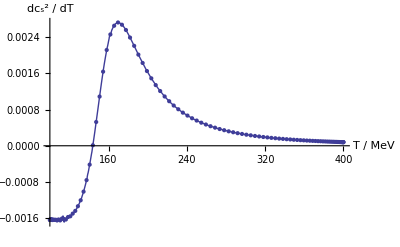

```mathematica
Show[Plot[cs2Try'[T],{T,100,400}],ListPlot[dcs2],AxesLabel->{"T / MeV","dc_s^2 / dT"}]
```

### Use the pseudospectral code to obtain all the derivatives

#### Set up the common definitions for all μ’s

```mathematica
NumPoints=100;
xj=Table[Cos[(π*(i-1))/NumPoints],{i,1,NumPoints+1}]//N;
Tj=250+150*xj;
pj=Table[If[(j==1)||(j==NumPoints+1),2,1],{j,1,NumPoints+1}];
δij=IdentityMatrix[NumPoints+1];
δij[[1,1]]=(1+2 NumPoints^2)/6;
δij[[NumPoints+1,NumPoints+1]]=-(1+2 NumPoints^2)/6;
Do[δij[[j,j]]=(-xj[[j]])/(2(1-xj[[j]]^2)),{j,2,NumPoints}];Do[If[i≠j,δij[[i,j]]=(-1)^(i+j)*pj[[i]]/(pj[[j]]*(xj[[i]]-xj[[j]]))],{i,1,NumPoints+1},{j,1,NumPoints+1}];
```

#### Loop over all μ

```mathematica
Do[
dcs2Local=Table[{Tj[[i]],1/150*Sum[δij[[i,j]]cs2Int[k][Tj[[j]]],{j,1,NumPoints+1}]},{i,1,NumPoints+1,Quotient[NumPoints,100]}];
dcs2Int[k]=Interpolation[dcs2Local];
,{k,1,5}]
```

#### See how good we did

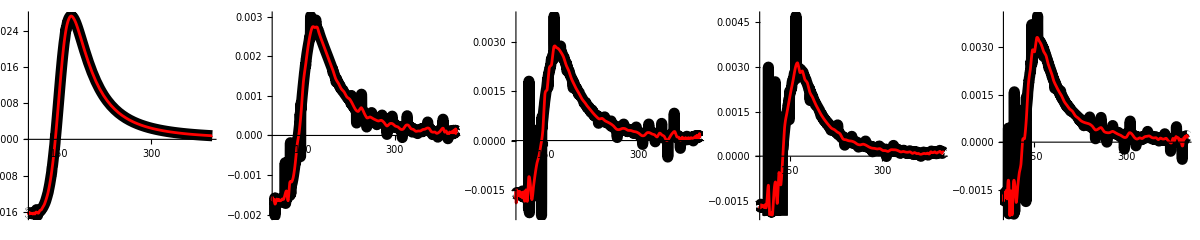

```mathematica
CompPlot[i_]:=Plot[{cs2Int[i]'[T],dcs2Int[i][T]},{T,100,400},PlotStyle->{{Thickness[0.02],Black},{Thickness[0.005],Red}}]
GraphicsGrid[{Table[CompPlot[i],{i,1,5}]},ImageSize->1200]
```

### Find fit to Janik’s formula

#### We’ll do the fitting over the following list of temperature values (in MeV)

```mathematica
TData=Table[T,{T,105,395,5}];
```

#### Fit the formula for all μ

```mathematica
Do[
Data=Table[{cs2Int[i][T]-1/3,T*dcs2Int[i][T],LHSInt[i][T]},{T,TData}];
NLM=NonlinearModelFit[Data,γ1*f1+γ2*f2,{γ1,γ2},{f1,f2}];
BestVals[i]=NLM[[1,2]];
,{i,1,5}];
```

#### Let’s look at the coefficients as a function of μ

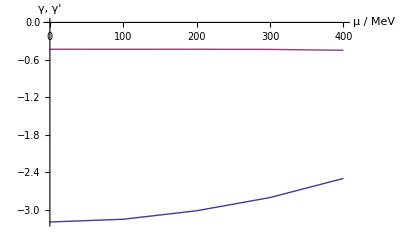

```mathematica
γList=Table[{(i-1)*100,γ1/.BestVals[i]},{i,1,5}];
γPList=Table[{(i-1)*100,γ2/.BestVals[i]},{i,1,5}];
ListPlot[{γList,γPList},Joined->True,AxesLabel->{"μ / MeV","γ, γ'"}]
```

#### Let’s see how good the fits are

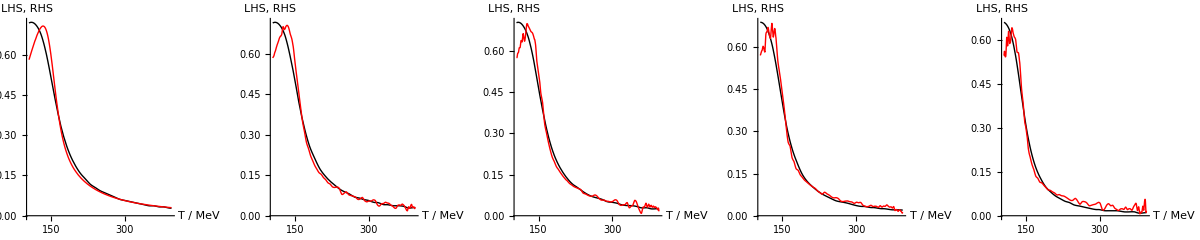

```mathematica
Do[RHS[i]=γ1*(cs2Int[i][TT]-1/3)+γ2*(TT*dcs2Int[i][TT])/.BestVals[i];,{i,1,5}]
GraphicsGrid[{Table[
Plot[{LHSInt[i][TT],RHS[i]},{TT,105,395},PlotStyle->{{Thick,Black},{Thick,Red}},AxesLabel->{"T / MeV","LHS, RHS"}],
{i,1,5}]},ImageSize->1200]
```

## Code for nonzero k, rough grid

### Prepare the code and select value of k

#### Select range of backrounds one is interested in -- we’ll be looking at four extreme backgrounds that span the parameter space

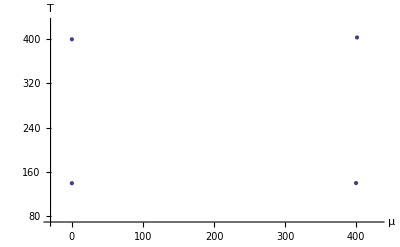

```mathematica
BkgOfInterest=Table[iTemp,{iTemp,{5,31,129,155}}];
ListPlot[Table[{DataIC[[BkgOfInterest[[iTemp]],1]],DataIC[[BkgOfInterest[[iTemp]],4]]},{iTemp,1,Length[BkgOfInterest],1}],PlotRange->{{-30,430},{70,430}},AxesLabel->{"μ","T"},AxesOrigin->{-30,70}]
```

#### Find the numerical k’s (in the untilded gauge) that correspond to k / 2 pi T being 1,2,3,4,5, and so on

```mathematica
kPlotList={0,1,2,3,4,5,0.5,1.5,2.5,3.5,4.5,0.25,0.75,1.25,1.75};
Do[
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=DataIC[[iTemp,2]];
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=DataIC[[iTemp,3]]* boundPhi1;

sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax},AccuracyGoal->60];
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];
tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4));
A0far=fitA[[1,2]];
kNumList[iTemp]=kPlotList*(2π*DataIC[[iTemp,4]])/lambda*phiA^(1/ν);
,{iTemp,BkgOfInterest}]
```

#### Select a specific k

```mathematica
kNum=15;
kPlotList[[kNum]]
```

1.75

#### Set up the grid -- notice that this needs to be changed as we increase k

```mathematica
ImωMin=-2;ImωMax=-0.1;ImωStep=0.03;
ReωMin=0.1;ReωMax=2;ReωStep=0.03;
NSteps=Length[Flatten[Table[1,{ReωLocal,ReωMin,ReωMax,ReωStep},{ImωLocal,ImωMin,ImωMax,ImωStep}]]]
```

4096

#### Save the limits for Reω, as we go through the k-list

```mathematica
ReωMinList={0.1,0.1,0.1,1,1,1.7,0.1,0.1,1.33,1.75,2.23,0.1,0.1,0.1,0.1};
ReωMaxList={2,2,2,3,3,3.7,2,2,1.75,2.23,2.69,2,2,2,2};
```

### Solve QNM for all the backgrounds

#### Run the code

```mathematica
Counter=1;
ProgressIndicator[Dynamic[ReωLocal],{ReωMin,ReωMax}]
Grid[{{"Background: ",Dynamic[Counter]," / ",Length[BkgOfInterest]}}]
Clear[Abss];
Do[
(* ----------------------------------------------------------------------------- *)
(* ---------- Solve for the bacgkround ----------------------------------------- *)
(* ----------------------------------------------------------------------------- *)
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=DataIC[[iTemp,2]];
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=DataIC[[iTemp,3]]* boundPhi1;

sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax},AccuracyGoal->60];
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];
tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4));
A0far=fitA[[1,2]];
(* ------------------------------------------------------------------------------- *)
(* ---------- Step up the QNM equation ------------------------------------------- *)
(* ------------------------------------------------------------------------------- *)
KGSimp=ⅇ^(-A[r])OnShellBox/.k->kNumList[iTemp][[kNum]]//Simplify;
hSerRul={h->Function[r,0+1*r+Ch2*r^2]};
ASerRul={A->Function[r,0+CA1*r+CA2*r^2]};
ψSerRul={ψ->Function[r,ψ0+ψ1*r+ψ2*r^2]};
ψ1Rule=Solve[(Series[KGSimp/.hSerRul/.ASerRul/.ψSerRul,{r,0,0}]//Normal)==0,ψ1][[1]];
CA1Rule={CA1->A1};
ωRule={ω->Reω+ⅈ*Imω};
ψ1Num=ψ1/.ψ1Rule/.ψ0->1/.CA1Rule/.ωRule;
(* ------------------------------------------------------------------------------- *)
(* ---------- The code ----------------------------------------------------------- *)
(* ------------------------------------------------------------------------------- *)
Res={};Ims={};Counter=0;
Do[
llSol=NDSolve[{
(KGSimp/.A->Function[r,Asol[r]]/.h->Function[r,hsol[r]]/.ωRule/.Reω->ReωLocal/.Imω->ImωLocal/.ψ->ll)==0,
ll[rstart]==1,ll'[rstart]==(ψ1Num/.Reω->ReωLocal/.Imω->ImωLocal)},
ll,{r,rstart,rmax}][[1]];
Res=Append[Res,{ReωLocal,ImωLocal,Re[ll[0.98rmax]/.llSol]}];
Ims=Append[Ims,{ReωLocal,ImωLocal,Im[ll[0.98rmax]/.llSol]}];
,{ReωLocal,ReωMin,ReωMax,ReωStep},{ImωLocal,ImωMin,ImωMax,ImωStep}];
(* -------------------------------------------------------------------------------- *)
(* ---------- Save the results ---------------------------------------------------- *)
(* -------------------------------------------------------------------------------- *)
Abss=Table[√(Res[[i,3]]^2+Ims[[i,3]]^2),{i,1,Length[Res]}];
Export["Data/Abs"<>ToString[iTemp]<>"kNum"<>ToString[kNum]<>".dat",Abss];
Counter=Counter+1;
,{iTemp,BkgOfInterest}]
```

### Find max value of ψ for clear clusters

```mathematica
Do[LimList[i]=0,{i,1,500}];
```

#### As before, select the background and find cluster centers for this specific k

```mathematica
kNum=15;
iTemp=BkgOfInterest[[4]];
Abss=Flatten[Import["Data/Abs"<>ToString[iTemp]<>"kNum"<>ToString[kNum]<>".dat"]];
MinVal=Min[Abss];
ωList=Flatten[Table[{ReωLocal,ImωLocal},{ReωLocal,ReωMin,ReωMax,ReωStep},{ImωLocal,ImωMin,ImωMax,ImωStep}],1];
Manipulate[
Lim=LimCoeff*MinVal;
AbsFine={};AbsValFine={};
Do[
If[Abss[[i]]<Lim,{
AbsFine=Append[AbsFine,{ωList[[i,1]],ωList[[i,2]]}];
AbsValFine=Append[AbsValFine,{Abss[[i]]}];
}];
,{i,1,Length[Abss]}];
ScatPlot=Show[Graphics[
Table[{PointSize[Medium],ColorData["SolarColors"]@(AbsValFine[[i,1]]/Lim),Point[AbsFine[[i]]]},{i,1,Length[AbsFine]}],Axes->True,PlotRange->{{ReωMin-0.1(ReωMax-ReωMin),ReωMax+0.1(ReωMax-ReωMin)},{ImωMin-0.1(ImωMax-ImωMin),ImωMax+0.1(ImωMax-ImωMin)}},AxesOrigin->{ReωMin-0.1(ReωMax-ReωMin),ImωMax+0.1(ImωMax-ImωMin)},AspectRatio->0.7,ImageSize->600,AxesLabel->{"Reω","Imω"},PlotLabel->"All points with |ψ|<"<>ToString[Lim]],
Graphics[{Black,Dashed,Line[{{ReωMin,ImωMin},{ReωMin,ImωMax},{ReωMax,ImωMax},{ReωMax,ImωMin},{ReωMin,ImωMin}}]}]];
Grid[{{
ScatPlot,
Grid[Table[{ColorData["SolarColors"]@i,i*Lim},{i,1,0.1,-0.1}],Spacings->{0,0},Alignment->Left]}}]
,{{LimCoeff,15},1.1,40},Button["Save the limit",LimList[iTemp]=LimCoeff;]]
```

#### Save the limits

```mathematica
Lims=Table[{ii,LimList[ii]},{ii,BkgOfInterest}]
```

{{5,3.05},{31,4.45},{129,2.5},{155,1.35}}

```mathematica
(*Export["Data/Lims-kNum-15.dat",Lims];*)
```

### Plot Imω and Reω as a function of k for these backgrounds

#### Load the limits for various k’s

```mathematica
LimsAll=Table[Import["Data/Lims-kNum-"<>ToString[i]<>".dat"],{i,1,Length[kPlotList]}];
```

#### Load the the full data for all backgrounds and all k’s and, using the previously loaded limits, find the Imω and Reω (in the numerical gauge)

```mathematica
Do[ReωRoughList[j]={};ImωRoughList[j]={};,{j,1,4}];
Do[
LimsLocal=LimsAll[[i]];
ωRoughList=Flatten[Table[{ReωLocal,ImωLocal},{ReωLocal,ReωMinList[[i]],ReωMaxList[[i]],0.03},{ImωLocal,-2,-0.1,0.03}],1];
Do[
AbssRough=Flatten[Import["Data/Abs"<>ToString[BkgOfInterest[[j]]]<>"kNum"<>ToString[i]<>".dat"]];
MinVal=Min[AbssRough];
LimL=LimsLocal[[j,2]]*MinVal;
AbsFine={};
Do[If[AbssRough[[k]]<LimL,{AbsFine=Append[AbsFine,{ωRoughList[[k,1]],ωRoughList[[k,2]]}];}];,{k,1,Length[AbssRough]}];
ReωArrayStart=Sort[AbsFine][[1,1]];
ImωArrayStart=Sort[AbsFine][[1,2]];
ReωRoughList[j]=Append[ReωRoughList[j],{kPlotList[[i]],ReωArrayStart}];
ImωRoughList[j]=Append[ImωRoughList[j],{kPlotList[[i]],ImωArrayStart}];
,{j,1,4}]
,{i,1,Length[LimsAll]}]
```

#### Now we need to find the conversion factors for each of the four backgrounds that we need to use to convert ω to physical units

```mathematica
Cnt=1;
Do[
Clear[phi0,Vphi0,fphi0,boundPhi1,Phi1,A,h,ϕ,Φ,sol];
phi0=DataIC[[iTemp,2]];
Vphi0=1/L^2(-12 Cosh[γ phi0] (1+a phi0^2)^(1/4)+b2 phi0^2+b4 phi0^4+b6 phi0^6);
fphi0=c1 Sech[c2 phi0+c3]+c4 Exp[c5 phi0];
boundPhi1=√(-(2 Vphi0)/fphi0);
Phi1=DataIC[[iTemp,3]]* boundPhi1;

sol=NDSolve[{ode1==0,ode2==0,ode3==0,ode4==0,A[rstart]==Ahor,A'[rstart]==dAhor,h[rstart]==hhor,h'[rstart]==dhhor,ϕ[rstart]==ϕhor,ϕ'[rstart]==dϕhor,Φ[rstart]==Φhor,Φ'[rstart]==dΦhor},{A,h,ϕ,Φ},{r,rstart,rmax},AccuracyGoal->60];
Clear[Asol,hsol,ϕsol,Φsol,Rsol];
Asol[r_]=A[r]/.sol[[1,1]];
hsol[r_]=h[r]/.sol[[1,2]];
ϕsol[r_]=ϕ[r]/.sol[[1,3]];
Φsol[r_]=Φ[r]/.sol[[1,4]];
Rsol[r_]=-20 hsol[r] Asol'[r]^2-9 Asol'[r] hsol'[r]-8 hsol[r] Asol''[r]-hsol''[r];
Clear[tableϕ,fitϕ,phiA,plottableϕ,plotfitϕ,testphiA,tableA,fitA,A0far,plottableA,plotfitA,testA0far];
tableϕ=Table[{j,ϕsol[j]},{j,1,rmax,0.001}];
fitϕ=FindFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
testphiA=NonlinearModelFit[tableϕ,phiA Exp[-ν Asol[r]],{phiA},r];
tableA=Table[{j,Asol[j]},{j,1,rmax,0.001}];
fitA=FindFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
testA0far=NonlinearModelFit[tableA,r/(L Sqrt[hsol[rmax]])+A0far,{A0far},r];
Clear[phiA,h0far,Phi0far,Phi2far,A0far];
phiA=fitϕ[[1,2]];
h0far=hsol[rmax];
Phi0far=Φsol[rmax];
Phi2far=-(L Sqrt[h0far] fphi0 Phi1)/(2 (c1 Sech[c3]+c4));
A0far=fitA[[1,2]];
ConvFactor[Cnt]=phiA^(1/ν)*√h0far;
Temperature[Cnt]=DataIC[[iTemp,4]];
Cnt=Cnt+1;
,{iTemp,BkgOfInterest}]
```

#### Use the conversion factors to form Imω / 2πT and Reω / 2πT lists

```mathematica
Do[
ReωDimList[j]=Table[{Sort[ReωRoughList[j]][[i,1]],(Sort[ReωRoughList[j]][[i,2]])/ConvFactor[j]*lambda/(2*π*Temperature[j])},{i,1,Length[ReωRoughList[j]]}];
ImωDimList[j]=Table[{Sort[ImωRoughList[j]][[i,1]],(Sort[ImωRoughList[j]][[i,2]])/ConvFactor[j]*lambda/(2*π*Temperature[j])},{i,1,Length[ImωRoughList[j]]}];
,{j,1,4}]
```

#### And finally, plot them together

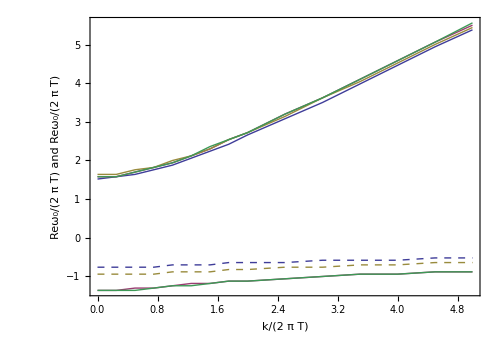

```mathematica
NonZeroK=Show[
ListPlot[Table[Sort[ReωDimList[j]],{j,1,4}],Joined->True,PlotStyle->Thick(*,PlotLegends->Placed[{"μ = 0 MeV, T = 140 MeV","μ = 0 MeV, T = 400 MeV","μ = 400 MeV, T = 140 MeV","μ = 400 MeV, T = 400 MeV"},{Scaled[{0.7,0.57}], {1.6, -0.4}}]*)],
ListPlot[Table[Sort[ImωDimList[j]],{j,1,4}],Joined->True,PlotStyle->{Dashed,Thick}],PlotRange->All,ImageSize->500,AspectRatio->0.7,AxesOrigin->{0,0},
Frame->True,Axes->False,LabelStyle->Directive[Black,12],RotateLabel->True,FrameLabel->{Style["k/(2  π T)",FontSize->14,Italic,Bold],Style["Reω_0/(2  π T)    and    Reω_0/(2  π T)",FontSize->14,Italic,Bold]}]
```

```mathematica
(*Export["NonZeroK.pdf",NonZeroK];*)
```